## day

```mathematica
szdirectory=".wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/";
shdirectory=".wine/drive_c/new_xdzq_tyrz/vipdoc/sh/lday/";
stock[str_]:=If[StringStartsQ[str,"sz"],szdirectory~~str~~".day",shdirectory~~str~~".day"];
```

```mathematica
head={"Day","O","H","L","C","Amount","Vol","Flag"};
data=BinaryReadList[stock["sz000002"],{"Integer32","Integer32","Integer32","Integer32","Integer32","Real32","Integer32","Integer32"}];
data[[All,6]]=IntegerPart[data[[All,6]]];
TableForm[data,TableHeadings->{None,head}]
```

Day | O | H | L | C | Amount | Vol | Flag
20130902 | 950 | 952 | 917 | 929 | 859782656 | 92254915 | 65536
20130903 | 935 | 973 | 925 | 971 | 1565224448 | 164005885 | 65536
20130904 | 965 | 975 | 960 | 963 | 743249216 | 76908308 | 65536
20130905 | 970 | 990 | 966 | 966 | 1034821504 | 105688315 | 65536
20130906 | 963 | 981 | 946 | 955 | 854607936 | 89402601 | 65536
20130909 | 957 | 1012 | 953 | 994 | 1922390144 | 194597012 | 65536
20130910 | 1000 | 1011 | 990 | 1008 | 1035078784 | 103608890 | 65536
20130911 | 1018 | 1045 | 1010 | 1023 | 1515592192 | 148168684 | 65536
20130912 | 1025 | 1038 | 997 | 1022 | 1273035008 | 125597432 | 65536
20130913 | 1021 | 1040 | 1010 | 1014 | 1133408000 | 110885693 | 65536
20130916 | 1021 | 1028 | 990 | 992 | 932470016 | 93173789 | 65536
20130917 | 997 | 997 | 959 | 960 | 1104007296 | 113583163 | 65536
20130918 | 960 | 966 | 956 | 963 | 607352704 | 63167950 | 65536
20130923 | 968 | 971 | 958 | 969 | 683878272 | 70982161 | 65536
20130924 | 962 | 963 | 936 | 940 | 1100583296 | 116562566 | 65536
20130925 | 940 | 940 | 915 | 919 | 1343309952 | 145011049 | 65536
20130926 | 920 | 925 | 899 | 901 | 1104822272 | 121394052 | 65536
20130927 | 902 | 908 | 895 | 906 | 628136064 | 69524583 | 65536
20130930 | 908 | 918 | 903 | 913 | 576146560 | 63375630 | 65536
20131008 | 911 | 960 | 901 | 955 | 1451175040 | 154685282 | 65536
20131009 | 950 | 951 | 932 | 939 | 798293888 | 85036560 | 65536
20131010 | 939 | 947 | 930 | 941 | 683140224 | 72710573 | 65536
20131011 | 945 | 948 | 935 | 944 | 755684992 | 80225709 | 65536
20131014 | 943 | 943 | 916 | 920 | 1077128704 | 116793089 | 65536
20131015 | 920 | 922 | 910 | 919 | 686715392 | 75066233 | 65536
20131016 | 914 | 921 | 902 | 907 | 579067264 | 63764717 | 65536
20131017 | 913 | 918 | 905 | 907 | 322699040 | 35453166 | 65536
20131018 | 909 | 920 | 902 | 917 | 447453280 | 48938199 | 65536
20131021 | 918 | 920 | 904 | 918 | 609910080 | 66814926 | 65536
20131022 | 916 | 917 | 905 | 908 | 568539520 | 62510306 | 65536
20131023 | 910 | 923 | 903 | 907 | 682986944 | 74875213 | 65536
20131024 | 900 | 917 | 884 | 896 | 643120704 | 71400847 | 65536
20131025 | 897 | 906 | 887 | 890 | 463207488 | 51716000 | 65536
20131028 | 895 | 895 | 871 | 873 | 487362880 | 55573519 | 65536
20131029 | 874 | 895 | 867 | 885 | 766292032 | 87113738 | 65536
20131030 | 897 | 910 | 878 | 908 | 830576640 | 92582855 | 65536
20131031 | 929 | 965 | 920 | 921 | 1845068032 | 195899610 | 65536
20131101 | 915 | 950 | 911 | 939 | 863300672 | 92113317 | 65536
20131104 | 948 | 949 | 918 | 920 | 497895328 | 53694682 | 65536
20131105 | 917 | 922 | 907 | 920 | 390671808 | 42789175 | 65536
20131106 | 915 | 916 | 900 | 902 | 556198592 | 61483870 | 65536
20131107 | 901 | 904 | 890 | 897 | 350915168 | 39130488 | 65536
20131108 | 895 | 905 | 885 | 887 | 409436704 | 45815309 | 65536
20131111 | 887 | 890 | 849 | 871 | 547722816 | 63161614 | 65536
20131112 | 870 | 884 | 866 | 881 | 382832096 | 43692619 | 65536
20131113 | 882 | 888 | 874 | 876 | 361462240 | 41039736 | 65536
20131114 | 883 | 888 | 857 | 869 | 530626784 | 61256991 | 65536
20131115 | 869 | 901 | 865 | 891 | 727417216 | 82040061 | 65536
20131118 | 892 | 921 | 883 | 920 | 1022804032 | 112926865 | 65536
20131119 | 919 | 919 | 903 | 908 | 582858944 | 64119879 | 65536
20131120 | 913 | 918 | 902 | 910 | 419314816 | 46224723 | 65536
20131121 | 900 | 900 | 871 | 883 | 813085184 | 92184386 | 65536
20131122 | 883 | 888 | 868 | 870 | 645570752 | 73831837 | 65536
20131125 | 860 | 869 | 850 | 861 | 679875136 | 79064459 | 65536
20131126 | 861 | 865 | 850 | 854 | 624122368 | 72815994 | 65536
20131127 | 854 | 860 | 848 | 856 | 557259776 | 65311128 | 65536
20131128 | 856 | 880 | 856 | 869 | 869718016 | 99854492 | 65536
20131129 | 870 | 884 | 866 | 876 | 731698944 | 83361067 | 65536
20131202 | 870 | 874 | 853 | 856 | 641639552 | 74523865 | 65536
20131203 | 855 | 869 | 849 | 865 | 519792352 | 60527890 | 65536
20131204 | 860 | 885 | 858 | 874 | 846575040 | 96920350 | 65536
20131205 | 874 | 884 | 869 | 874 | 570902336 | 65159192 | 65536
20131206 | 870 | 878 | 863 | 867 | 426051232 | 49028993 | 65536
20131209 | 869 | 874 | 859 | 862 | 366620320 | 42454623 | 65536
20131210 | 862 | 871 | 862 | 867 | 466805408 | 53895967 | 65536
20131211 | 862 | 865 | 852 | 854 | 471522336 | 54940027 | 65536
20131212 | 852 | 858 | 851 | 853 | 333275264 | 39013317 | 65536
20131213 | 850 | 860 | 849 | 854 | 350349280 | 40964879 | 65536
20131216 | 856 | 859 | 842 | 843 | 476422816 | 56120275 | 65536
20131217 | 845 | 846 | 825 | 827 | 555024128 | 66563250 | 65536
20131218 | 830 | 833 | 824 | 826 | 386769952 | 46767849 | 65536
20131219 | 828 | 832 | 811 | 814 | 480576896 | 58666409 | 65536
20131220 | 818 | 819 | 785 | 785 | 664027136 | 83183147 | 65536
20131223 | 786 | 790 | 772 | 779 | 503004128 | 64642037 | 65536
20131224 | 780 | 795 | 771 | 783 | 411131936 | 52440681 | 65536
20131225 | 783 | 793 | 776 | 791 | 357235008 | 45541441 | 65536
20131226 | 790 | 791 | 775 | 780 | 418330080 | 53486219 | 65536
20131227 | 785 | 810 | 781 | 803 | 590192384 | 73964223 | 65536
20131230 | 805 | 807 | 780 | 786 | 590734400 | 74705680 | 65536
20131231 | 779 | 807 | 774 | 803 | 574458880 | 72316396 | 65536
20140102 | 799 | 807 | 792 | 799 | 387391072 | 48529922 | 65536
20140103 | 797 | 797 | 776 | 784 | 424761280 | 54046703 | 65536
20140106 | 782 | 784 | 737 | 748 | 923778176 | 123159417 | 65536
20140107 | 743 | 751 | 734 | 743 | 446992736 | 60114910 | 65536
20140108 | 745 | 751 | 738 | 742 | 442046912 | 59453293 | 65536
20140109 | 743 | 752 | 735 | 746 | 608623744 | 81723447 | 65536
20140110 | 742 | 747 | 737 | 738 | 346476224 | 46769821 | 65536
20140113 | 739 | 742 | 706 | 724 | 853376896 | 118755434 | 65536
20140114 | 718 | 726 | 713 | 723 | 624901696 | 86962315 | 65536
20140115 | 721 | 723 | 712 | 717 | 352430048 | 49175339 | 65536
20140116 | 718 | 722 | 712 | 719 | 342032096 | 47695031 | 65536
20140117 | 717 | 718 | 708 | 708 | 396446912 | 55566776 | 65536
20140120 | 706 | 716 | 704 | 713 | 292738048 | 41191616 | 65536
20140121 | 715 | 727 | 715 | 722 | 346932384 | 48030688 | 65536
20140122 | 724 | 768 | 722 | 762 | 857607744 | 114057648 | 65536
20140123 | 764 | 766 | 743 | 749 | 591438656 | 78757310 | 65536
20140124 | 747 | 793 | 745 | 779 | 1058260864 | 136181576 | 65536
20140127 | 770 | 777 | 758 | 765 | 542034112 | 70673937 | 65536
20140128 | 770 | 779 | 753 | 764 | 324017088 | 42356651 | 65536
20140129 | 767 | 768 | 748 | 754 | 383233600 | 50799173 | 65536
20140130 | 752 | 752 | 736 | 738 | 290734048 | 39253866 | 65536
20140207 | 734 | 741 | 724 | 741 | 364212832 | 49853030 | 65536
20140210 | 745 | 755 | 742 | 751 | 795673024 | 106237990 | 65536
20140211 | 750 | 762 | 743 | 755 | 816144128 | 108444665 | 65536
20140212 | 753 | 761 | 749 | 752 | 630865792 | 83775437 | 65536
20140213 | 752 | 752 | 738 | 741 | 627264960 | 84305117 | 65536
20140214 | 741 | 745 | 730 | 737 | 700988608 | 95328746 | 65536
20140217 | 740 | 742 | 730 | 737 | 625666368 | 85133904 | 65536
20140218 | 736 | 736 | 726 | 727 | 571227264 | 78169462 | 65536
20140219 | 727 | 740 | 723 | 737 | 672856448 | 91851794 | 65536
20140220 | 737 | 748 | 730 | 732 | 665030720 | 90021801 | 65536
20140221 | 731 | 735 | 710 | 716 | 758288576 | 105234543 | 65536
20140224 | 700 | 701 | 662 | 669 | 1282595456 | 190424662 | 65536
20140225 | 670 | 674 | 655 | 657 | 860119104 | 129932467 | 65536
20140226 | 657 | 671 | 652 | 668 | 620173248 | 94190488 | 65536
20140227 | 671 | 672 | 655 | 659 | 524217760 | 79014200 | 65536
20140228 | 661 | 674 | 658 | 672 | 452668800 | 67940834 | 65536
20140303 | 667 | 671 | 656 | 664 | 503907232 | 76074355 | 65536
20140304 | 700 | 710 | 678 | 692 | 1467381120 | 212249601 | 65536
20140305 | 692 | 692 | 675 | 676 | 402549856 | 59026244 | 65536
20140306 | 676 | 743 | 669 | 732 | 1900909568 | 266097004 | 65536
20140307 | 734 | 746 | 723 | 727 | 1263703936 | 171953502 | 65536
20140310 | 722 | 733 | 704 | 715 | 837063104 | 116402600 | 65536
20140311 | 719 | 759 | 715 | 750 | 1412509440 | 189248809 | 65536
20140312 | 748 | 785 | 742 | 760 | 1603158784 | 208987285 | 65536
20140313 | 758 | 785 | 753 | 771 | 1149904000 | 149235872 | 65536
20140314 | 768 | 781 | 750 | 753 | 996213440 | 130310997 | 65536
20140317 | 760 | 780 | 759 | 776 | 908293056 | 117707900 | 65536
20140318 | 776 | 776 | 755 | 760 | 642680640 | 84389956 | 65536
20140319 | 751 | 754 | 724 | 750 | 1158670976 | 157546281 | 65536
20140320 | 750 | 773 | 740 | 751 | 876828992 | 115455187 | 65536
20140321 | 757 | 808 | 745 | 801 | 2118807040 | 270439501 | 65536
20140324 | 801 | 817 | 785 | 806 | 1122120960 | 139877099 | 65536
20140325 | 804 | 820 | 790 | 798 | 769251840 | 95754115 | 65536
20140326 | 799 | 804 | 779 | 785 | 553737792 | 70405842 | 65536
20140327 | 780 | 810 | 773 | 798 | 857121792 | 107800631 | 65536
20140328 | 793 | 824 | 792 | 812 | 896881728 | 110530999 | 65536
20140331 | 816 | 822 | 796 | 809 | 546825600 | 67897119 | 65536
20140401 | 808 | 818 | 805 | 808 | 426237408 | 52524942 | 65536
20140402 | 814 | 840 | 811 | 829 | 1069009792 | 128655948 | 65536
20140403 | 830 | 839 | 807 | 810 | 810649920 | 98636692 | 65536
20140404 | 810 | 815 | 801 | 811 | 519860640 | 64285871 | 65536
20140408 | 805 | 823 | 794 | 815 | 778608384 | 96118504 | 65536
20140409 | 816 | 819 | 802 | 805 | 749184320 | 92985418 | 65536
20140410 | 804 | 808 | 782 | 805 | 1271310080 | 160169456 | 65536
20140411 | 800 | 801 | 789 | 795 | 616719808 | 77595171 | 65536
20140414 | 795 | 801 | 783 | 793 | 419179424 | 53024683 | 65536
20140415 | 786 | 791 | 770 | 776 | 590811584 | 75881356 | 65536
20140416 | 774 | 792 | 771 | 787 | 557522112 | 70965625 | 65536
20140417 | 788 | 789 | 773 | 775 | 355678848 | 45759242 | 65536
20140418 | 770 | 780 | 762 | 778 | 316044512 | 41008279 | 65536
20140421 | 771 | 780 | 765 | 766 | 351633984 | 45448390 | 65536
20140422 | 765 | 777 | 762 | 774 | 498926816 | 64815843 | 65536
20140423 | 772 | 783 | 770 | 780 | 380461216 | 48885958 | 65536
20140424 | 783 | 810 | 777 | 799 | 1118052352 | 139640297 | 65536
20140425 | 807 | 811 | 790 | 794 | 558804672 | 69763109 | 65536
20140428 | 798 | 816 | 792 | 797 | 777834944 | 96845118 | 65536
20140429 | 791 | 798 | 767 | 794 | 524493504 | 67109783 | 65536
20140430 | 787 | 798 | 777 | 790 | 312451008 | 39547643 | 65536
20140505 | 785 | 786 | 767 | 774 | 446552192 | 57717483 | 65536
20140506 | 774 | 790 | 774 | 779 | 362147104 | 46379716 | 65536
20140507 | 779 | 789 | 775 | 787 | 413257728 | 52723015 | 65536
20140508 | 748 | 758 | 732 | 735 | 559315904 | 75190490 | 65536
20140509 | 735 | 737 | 710 | 726 | 455104576 | 62968012 | 65536
20140512 | 728 | 743 | 719 | 732 | 378905120 | 51722748 | 65536
20140513 | 739 | 759 | 737 | 753 | 674165056 | 89727866 | 65536
20140514 | 765 | 783 | 761 | 763 | 717443072 | 93198701 | 65536
20140515 | 762 | 764 | 753 | 758 | 347998496 | 45869870 | 65536
20140516 | 758 | 780 | 758 | 770 | 742805248 | 96234169 | 65536
20140519 | 766 | 778 | 752 | 769 | 455281152 | 59464663 | 65536
20140520 | 770 | 778 | 764 | 774 | 530138272 | 68587514 | 65536
20140521 | 768 | 777 | 758 | 774 | 417012736 | 54343526 | 65536
20140522 | 775 | 794 | 773 | 789 | 726170176 | 92142006 | 65536
20140523 | 792 | 820 | 785 | 815 | 1079426688 | 133827747 | 65536
20140526 | 820 | 829 | 807 | 811 | 494191840 | 60755644 | 65536
20140527 | 811 | 825 | 806 | 817 | 655534272 | 80099743 | 65536
20140528 | 818 | 846 | 817 | 845 | 1298336256 | 155707433 | 65536
20140529 | 860 | 875 | 844 | 854 | 1426865280 | 166699697 | 65536
20140530 | 858 | 866 | 848 | 855 | 907940480 | 106158847 | 65536
20140603 | 851 | 863 | 832 | 840 | 997159552 | 118452510 | 65536
20140604 | 836 | 840 | 812 | 820 | 636734912 | 77377164 | 65536
20140605 | 818 | 835 | 815 | 831 | 392857152 | 47658634 | 65536
20140606 | 831 | 833 | 809 | 825 | 405369920 | 49519123 | 65536
20140609 | 817 | 856 | 812 | 830 | 693052736 | 82674296 | 65536
20140610 | 825 | 849 | 825 | 839 | 581961408 | 69509520 | 65536
20140611 | 838 | 852 | 832 | 840 | 489075968 | 57966817 | 65536
20140612 | 839 | 846 | 820 | 841 | 665178176 | 80101101 | 65536
20140613 | 838 | 848 | 828 | 843 | 533383904 | 63554128 | 65536
20140616 | 841 | 842 | 818 | 826 | 713535168 | 86351325 | 65536
20140617 | 825 | 825 | 804 | 812 | 554925824 | 68598640 | 65536
20140618 | 812 | 817 | 807 | 810 | 281499488 | 34636546 | 65536
20140619 | 813 | 815 | 797 | 799 | 326318464 | 40521829 | 65536
20140620 | 804 | 813 | 799 | 813 | 344097088 | 42668277 | 65536
20140623 | 813 | 818 | 808 | 815 | 202745888 | 24932778 | 65536
20140624 | 819 | 819 | 805 | 809 | 263219952 | 32425074 | 65536
20140625 | 813 | 814 | 796 | 813 | 431750720 | 53653821 | 65536
20140626 | 812 | 833 | 809 | 826 | 493632448 | 59903477 | 65536
20140627 | 827 | 838 | 823 | 832 | 457646880 | 55083158 | 65536
20140630 | 832 | 835 | 822 | 827 | 325828960 | 39373646 | 65536
20140701 | 829 | 829 | 806 | 810 | 494620512 | 60936886 | 65536
20140702 | 809 | 813 | 805 | 812 | 328887456 | 40633122 | 65536
20140703 | 811 | 817 | 810 | 815 | 234449792 | 28803744 | 65536
20140704 | 820 | 850 | 820 | 847 | 1137610368 | 135819314 | 65536
20140707 | 850 | 889 | 845 | 876 | 1279446400 | 146016750 | 65536
20140708 | 875 | 878 | 856 | 868 | 549020864 | 63437524 | 65536
20140709 | 869 | 876 | 854 | 856 | 539971328 | 62359504 | 65536
20140710 | 858 | 876 | 858 | 869 | 434251264 | 49893452 | 65536
20140711 | 886 | 894 | 874 | 881 | 753337600 | 84999231 | 65536
20140714 | 879 | 897 | 875 | 888 | 456768832 | 51388299 | 65536
20140715 | 886 | 890 | 884 | 886 | 333194464 | 37598053 | 65536
20140716 | 885 | 893 | 867 | 870 | 643863936 | 73163862 | 65536
20140717 | 869 | 875 | 847 | 861 | 606426560 | 70507173 | 65536
20140718 | 853 | 902 | 851 | 889 | 911236800 | 102544984 | 65536
20140721 | 890 | 899 | 888 | 894 | 460833376 | 51590098 | 65536
20140722 | 890 | 921 | 888 | 918 | 798481792 | 87526655 | 65536
20140723 | 918 | 946 | 918 | 939 | 833888064 | 89243275 | 65536
20140724 | 942 | 982 | 942 | 977 | 1391582336 | 143246839 | 65536
20140725 | 982 | 989 | 957 | 981 | 718195328 | 73857325 | 65536
20140728 | 981 | 1000 | 971 | 985 | 1203056128 | 122006964 | 65536
20140729 | 984 | 1009 | 970 | 1000 | 1049519296 | 106660622 | 65536
20140730 | 993 | 1001 | 949 | 963 | 1576620288 | 163303506 | 65536
20140731 | 958 | 992 | 949 | 990 | 897485568 | 92241870 | 65536
20140801 | 980 | 998 | 973 | 974 | 887076736 | 90307554 | 65536
20140804 | 975 | 997 | 967 | 995 | 891646208 | 90638324 | 65536
20140805 | 997 | 997 | 967 | 974 | 802120576 | 82225446 | 65536
20140806 | 968 | 969 | 947 | 958 | 731466432 | 76684200 | 65536
20140807 | 956 | 965 | 948 | 952 | 659892096 | 69168170 | 65536
20140808 | 952 | 954 | 930 | 944 | 825820032 | 87785520 | 65536
20140811 | 944 | 968 | 944 | 961 | 674648768 | 70199816 | 65536
20140812 | 961 | 961 | 950 | 956 | 493666048 | 51742768 | 65536
20140813 | 961 | 963 | 940 | 955 | 506251136 | 53130832 | 65536
20140814 | 954 | 957 | 935 | 936 | 591453888 | 62663972 | 65536
20140815 | 935 | 950 | 935 | 940 | 393850784 | 41807899 | 65536
20140818 | 941 | 948 | 935 | 938 | 551229504 | 58681054 | 65536
20140819 | 943 | 943 | 933 | 940 | 544880256 | 58195383 | 65536
20140820 | 939 | 939 | 918 | 921 | 865292032 | 93599027 | 65536
20140821 | 918 | 934 | 902 | 933 | 892389824 | 97301143 | 65536
20140822 | 926 | 937 | 924 | 935 | 542859584 | 58237096 | 65536
20140825 | 933 | 933 | 911 | 916 | 488992672 | 53218239 | 65536
20140826 | 910 | 922 | 908 | 916 | 320373984 | 34970733 | 65536
20140827 | 916 | 926 | 911 | 916 | 305748064 | 33304074 | 65536
20140828 | 916 | 918 | 901 | 902 | 463319168 | 51021812 | 65536
20140829 | 905 | 915 | 902 | 912 | 287416192 | 31654038 | 65536
20140901 | 912 | 919 | 910 | 917 | 398975840 | 43650716 | 65536
20140902 | 919 | 925 | 911 | 925 | 560099392 | 61047053 | 65536
20140903 | 926 | 952 | 925 | 950 | 1103831808 | 117016905 | 65536
20140904 | 965 | 977 | 960 | 967 | 1065268160 | 110023968 | 65536
20140905 | 971 | 986 | 968 | 983 | 904674944 | 92477194 | 65536
20140909 | 983 | 983 | 958 | 962 | 608209600 | 63020147 | 65536
20140910 | 951 | 954 | 935 | 946 | 651449280 | 69121083 | 65536
20140911 | 942 | 958 | 939 | 944 | 666584832 | 70468191 | 65536
20140912 | 940 | 946 | 934 | 944 | 364837600 | 38822784 | 65536
20140915 | 936 | 936 | 920 | 925 | 889241216 | 96156045 | 65536
20140916 | 929 | 934 | 921 | 921 | 732481664 | 79017359 | 65536
20140917 | 927 | 930 | 922 | 927 | 625744448 | 67567134 | 65536
20140918 | 922 | 928 | 917 | 923 | 597581056 | 64854472 | 65536
20140919 | 923 | 928 | 918 | 928 | 609410880 | 66069087 | 65536
20140922 | 926 | 932 | 919 | 922 | 617774592 | 66823025 | 65536
20140923 | 934 | 950 | 928 | 933 | 823702592 | 87944015 | 65536
20140924 | 930 | 945 | 926 | 944 | 842009408 | 89800368 | 65536
20140925 | 949 | 952 | 936 | 939 | 743524096 | 78939072 | 65536
20140926 | 938 | 941 | 928 | 933 | 506336512 | 54349142 | 65536
20140929 | 933 | 933 | 915 | 922 | 804914944 | 87374168 | 65536
20140930 | 921 | 923 | 915 | 918 | 476490368 | 51921854 | 65536
20141008 | 954 | 958 | 935 | 944 | 1368339584 | 144731249 | 65536
20141009 | 945 | 957 | 945 | 947 | 783407424 | 82505043 | 65536
20141010 | 947 | 971 | 941 | 957 | 1131702784 | 117857898 | 65536
20141013 | 957 | 980 | 950 | 964 | 799998976 | 82853651 | 65536
20141014 | 963 | 963 | 945 | 951 | 623317312 | 65439841 | 65536
20141015 | 946 | 952 | 930 | 941 | 572109120 | 60905973 | 65536
20141016 | 935 | 938 | 928 | 931 | 567120640 | 60828971 | 65536
20141017 | 931 | 941 | 926 | 935 | 552794432 | 59139585 | 65536
20141020 | 940 | 946 | 932 | 935 | 559934848 | 59740208 | 65536
20141021 | 933 | 934 | 920 | 922 | 511264672 | 55151266 | 65536
20141022 | 923 | 928 | 918 | 920 | 380052416 | 41200588 | 65536
20141023 | 921 | 924 | 904 | 910 | 437630464 | 47805853 | 65536
20141024 | 909 | 918 | 905 | 909 | 296068288 | 32534390 | 65536
20141027 | 908 | 909 | 874 | 878 | 744718976 | 84247692 | 65536
20141028 | 882 | 903 | 882 | 902 | 617348864 | 69320055 | 65536
20141029 | 903 | 922 | 892 | 922 | 760959296 | 83736558 | 65536
20141030 | 922 | 922 | 907 | 918 | 632422208 | 69282091 | 65536
20141031 | 916 | 942 | 915 | 940 | 1026129152 | 110085337 | 65536
20141103 | 943 | 956 | 920 | 930 | 830074304 | 88453872 | 65536
20141104 | 926 | 942 | 918 | 939 | 841437760 | 90586942 | 65536
20141105 | 938 | 941 | 925 | 929 | 445495808 | 47882654 | 65536
20141106 | 932 | 950 | 929 | 933 | 680029760 | 72446948 | 65536
20141107 | 934 | 956 | 925 | 940 | 942274048 | 100219593 | 65536
20141110 | 950 | 962 | 944 | 958 | 1232898816 | 129161814 | 65536
20141111 | 963 | 980 | 956 | 960 | 1607690112 | 166241473 | 65536
20141112 | 958 | 974 | 954 | 971 | 915589248 | 94738670 | 65536
20141113 | 972 | 977 | 945 | 951 | 950344128 | 99145624 | 65536
20141114 | 948 | 969 | 940 | 967 | 941655552 | 98173822 | 65536
20141117 | 970 | 984 | 940 | 947 | 954597760 | 99617708 | 65536
20141118 | 943 | 948 | 923 | 929 | 661328384 | 70960776 | 65536
20141119 | 925 | 932 | 915 | 919 | 667606272 | 72505125 | 65536
20141120 | 915 | 927 | 914 | 924 | 534251744 | 57962549 | 65536
20141121 | 923 | 938 | 918 | 937 | 737516864 | 79580232 | 65536
20141124 | 990 | 1030 | 975 | 1015 | 4708755968 | 469876708 | 65536
20141125 | 1015 | 1022 | 995 | 1008 | 1878702080 | 186713202 | 65536
20141126 | 1008 | 1015 | 994 | 1010 | 1901560448 | 189055113 | 65536
20141127 | 1014 | 1045 | 1003 | 1027 | 2215513856 | 216268292 | 65536
20141128 | 1020 | 1100 | 1011 | 1090 | 3502931712 | 332032901 | 65536
20141201 | 1090 | 1099 | 1061 | 1064 | 2216246528 | 205976774 | 65536
20141202 | 1054 | 1115 | 1046 | 1093 | 2542842880 | 235322863 | 65536
20141203 | 1100 | 1188 | 1100 | 1120 | 3901968384 | 340833803 | 65536
20141204 | 1121 | 1180 | 1103 | 1169 | 2660987648 | 232218028 | 65536
20141205 | 1173 | 1210 | 1110 | 1146 | 3617616896 | 312328425 | 65536
20141208 | 1145 | 1253 | 1130 | 1230 | 4304524288 | 359270797 | 65536
20141209 | 1200 | 1320 | 1128 | 1142 | 5655065600 | 456768908 | 65536
20141210 | 1158 | 1208 | 1126 | 1195 | 3132378624 | 267254905 | 65536
20141211 | 1180 | 1245 | 1168 | 1203 | 2225831168 | 184410098 | 65536
20141212 | 1203 | 1215 | 1150 | 1169 | 1546874752 | 131025884 | 65536
20141215 | 1155 | 1156 | 1108 | 1130 | 1882178176 | 167788363 | 65536
20141216 | 1122 | 1153 | 1108 | 1153 | 2301756672 | 203807940 | 65536
20141217 | 1150 | 1196 | 1126 | 1193 | 3550821120 | 305553401 | 65536
20141218 | 1201 | 1228 | 1155 | 1162 | 2874781696 | 241689311 | 65536
20141219 | 1162 | 1163 | 1118 | 1148 | 2075060480 | 182246098 | 65536
20141222 | 1150 | 1218 | 1131 | 1172 | 3266151424 | 276651532 | 65536
20141223 | 1170 | 1220 | 1135 | 1175 | 3420035584 | 286011890 | 65536
20141224 | 1172 | 1175 | 1093 | 1103 | 3056208384 | 271519365 | 65536
20141225 | 1108 | 1128 | 1094 | 1122 | 1795369856 | 161341126 | 65536
20141226 | 1123 | 1181 | 1118 | 1178 | 2964825088 | 257646232 | 65536
20141229 | 1203 | 1286 | 1188 | 1243 | 6751927296 | 543748334 | 65536
20141230 | 1245 | 1315 | 1219 | 1264 | 4894974976 | 386124422 | 65536
20141231 | 1260 | 1390 | 1246 | 1390 | 6494929920 | 489954459 | 65536
20150105 | 1439 | 1529 | 1422 | 1491 | 9700711424 | 656083570 | 65536
20150106 | 1460 | 1499 | 1405 | 1436 | 4839616000 | 334634683 | 65536
20150107 | 1426 | 1450 | 1400 | 1423 | 3772150784 | 264205133 | 65536
20150108 | 1432 | 1437 | 1346 | 1359 | 3629554176 | 263939418 | 65536
20150109 | 1354 | 1422 | 1329 | 1345 | 4521978368 | 329458430 | 65536
20150112 | 1332 | 1332 | 1275 | 1312 | 3180963072 | 243634136 | 65536
20150113 | 1305 | 1338 | 1297 | 1307 | 2187988224 | 166461033 | 65536
20150114 | 1307 | 1330 | 1287 | 1310 | 2160267776 | 164681802 | 65536
20150115 | 1313 | 1383 | 1300 | 1377 | 3265536000 | 242968664 | 65536
20150116 | 1377 | 1377 | 1339 | 1352 | 2892247296 | 212947597 | 65536
20150119 | 1250 | 1290 | 1217 | 1217 | 4483884544 | 360362565 | 65536
20150120 | 1220 | 1260 | 1206 | 1235 | 3604938240 | 291468879 | 65536
20150121 | 1233 | 1320 | 1210 | 1305 | 4554003968 | 355529415 | 65536
20150122 | 1302 | 1365 | 1292 | 1358 | 4326297600 | 322472724 | 65536
20150123 | 1357 | 1409 | 1330 | 1392 | 4561752576 | 331040858 | 65536
20150126 | 1399 | 1400 | 1344 | 1370 | 2957275904 | 216268529 | 65536
20150127 | 1367 | 1372 | 1286 | 1318 | 3704808960 | 280401840 | 65536
20150128 | 1311 | 1327 | 1288 | 1300 | 2035823360 | 156174324 | 65536
20150129 | 1270 | 1317 | 1262 | 1301 | 1903301504 | 146830314 | 65536
20150130 | 1309 | 1349 | 1280 | 1312 | 2753102080 | 209624706 | 65536
20150202 | 1279 | 1339 | 1248 | 1288 | 2560710656 | 197676082 | 65536
20150203 | 1291 | 1313 | 1230 | 1296 | 3721989120 | 293687163 | 65536
20150204 | 1290 | 1316 | 1277 | 1280 | 2153610240 | 166087204 | 65536
20150205 | 1339 | 1353 | 1268 | 1270 | 4154456576 | 316036059 | 65536
20150206 | 1262 | 1262 | 1198 | 1216 | 3875290880 | 316318643 | 65536
20150209 | 1203 | 1233 | 1174 | 1218 | 1545255552 | 127802405 | 65536
20150210 | 1211 | 1247 | 1205 | 1242 | 1331390464 | 107745646 | 65536
20150211 | 1250 | 1264 | 1234 | 1241 | 1095982336 | 87832923 | 65536
20150212 | 1241 | 1255 | 1220 | 1247 | 1109421056 | 89526728 | 65536
20150213 | 1254 | 1301 | 1233 | 1276 | 2503342336 | 196804327 | 65536
20150216 | 1266 | 1276 | 1253 | 1264 | 1650830592 | 130814481 | 65536
20150217 | 1271 | 1283 | 1262 | 1277 | 1525915136 | 119878310 | 65536
20150225 | 1277 | 1277 | 1233 | 1240 | 1867537024 | 149805183 | 65536
20150226 | 1240 | 1285 | 1235 | 1285 | 2189347840 | 173376273 | 65536
20150227 | 1277 | 1297 | 1269 | 1275 | 1594683008 | 124631861 | 65536
20150302 | 1302 | 1310 | 1263 | 1277 | 4151867648 | 322563394 | 65536
20150303 | 1262 | 1263 | 1216 | 1220 | 2928813312 | 236553541 | 65536
20150304 | 1220 | 1238 | 1204 | 1222 | 2005295616 | 164713763 | 65536
20150305 | 1209 | 1216 | 1181 | 1190 | 2147302400 | 179378693 | 65536
20150306 | 1190 | 1213 | 1188 | 1194 | 1324128256 | 110503684 | 65536
20150309 | 1180 | 1236 | 1153 | 1222 | 2433768448 | 204422896 | 65536
20150310 | 1209 | 1216 | 1197 | 1202 | 1297837440 | 107710986 | 65536
20150311 | 1202 | 1220 | 1187 | 1193 | 1388717696 | 115373366 | 65536
20150312 | 1206 | 1229 | 1196 | 1222 | 2208554496 | 181872852 | 65536
20150313 | 1227 | 1240 | 1216 | 1223 | 1637332992 | 133406973 | 65536
20150316 | 1236 | 1253 | 1226 | 1249 | 2175852288 | 175378183 | 65536
20150317 | 1259 | 1274 | 1251 | 1263 | 2687890432 | 212834913 | 65536
20150318 | 1265 | 1320 | 1265 | 1314 | 3741533952 | 289546776 | 65536
20150319 | 1308 | 1308 | 1276 | 1287 | 2747447040 | 212978891 | 65536
20150320 | 1295 | 1335 | 1278 | 1314 | 4561069568 | 349401617 | 65536
20150323 | 1330 | 1365 | 1326 | 1336 | 4458518528 | 331361197 | 65536
20150324 | 1337 | 1338 | 1286 | 1305 | 3473050112 | 265616943 | 65536
20150325 | 1304 | 1304 | 1269 | 1278 | 2661617408 | 207376123 | 65536
20150326 | 1269 | 1305 | 1257 | 1295 | 2680422912 | 209000774 | 65536
20150327 | 1318 | 1335 | 1302 | 1335 | 4549707264 | 344158989 | 65536
20150330 | 1340 | 1448 | 1318 | 1424 | 8775743488 | 636164786 | 65536
20150331 | 1485 | 1497 | 1365 | 1382 | 10756474880 | 748147370 | 65536
20150401 | 1373 | 1386 | 1347 | 1372 | 5137432576 | 375803467 | 65536
20150402 | 1376 | 1392 | 1343 | 1359 | 4366632960 | 319924638 | 65536
20150403 | 1341 | 1348 | 1319 | 1345 | 4752985088 | 356563188 | 65536
20150407 | 1348 | 1373 | 1337 | 1372 | 5085149696 | 375319504 | 65536
20150408 | 1372 | 1392 | 1341 | 1382 | 6141003264 | 448981516 | 65536
20150409 | 1383 | 1482 | 1351 | 1464 | 10099959808 | 717154662 | 65536
20150410 | 1428 | 1447 | 1407 | 1432 | 6067355136 | 424894210 | 65536
20150413 | 1442 | 1462 | 1422 | 1437 | 5872259584 | 407430546 | 65536
20150414 | 1433 | 1446 | 1400 | 1412 | 4665719808 | 327675989 | 65536
20150415 | 1410 | 1418 | 1381 | 1390 | 3903055616 | 278402259 | 65536
20150416 | 1384 | 1430 | 1377 | 1430 | 4722539520 | 334623330 | 65536
20150417 | 1452 | 1492 | 1431 | 1467 | 8532838400 | 584609275 | 65536
20150420 | 1478 | 1510 | 1419 | 1421 | 8718400512 | 593316479 | 65536
20150421 | 1416 | 1455 | 1402 | 1448 | 5334590976 | 374324313 | 65536
20150422 | 1450 | 1492 | 1441 | 1488 | 6569892864 | 446876301 | 65536
20150423 | 1515 | 1525 | 1465 | 1476 | 7047246336 | 471733124 | 65536
20150424 | 1448 | 1470 | 1415 | 1442 | 5206488064 | 362066189 | 65536
20150427 | 1441 | 1470 | 1430 | 1470 | 6143012352 | 422562029 | 65536
20150428 | 1465 | 1466 | 1411 | 1419 | 5550367744 | 386603904 | 65536
20150429 | 1407 | 1443 | 1393 | 1424 | 3925805312 | 277332899 | 65536
20150430 | 1433 | 1493 | 1421 | 1460 | 7892159488 | 541148626 | 65536
20150504 | 1462 | 1479 | 1440 | 1455 | 4513107968 | 309176805 | 65536
20150505 | 1461 | 1463 | 1362 | 1377 | 4628568576 | 328552431 | 65536
20150506 | 1383 | 1405 | 1341 | 1356 | 3476236288 | 252171903 | 65536
20150507 | 1354 | 1378 | 1348 | 1361 | 2387227392 | 175422281 | 65536
20150508 | 1370 | 1381 | 1347 | 1380 | 2706847232 | 197857505 | 65536
20150511 | 1400 | 1410 | 1381 | 1407 | 5107136000 | 365307474 | 65536
20150512 | 1404 | 1404 | 1383 | 1392 | 3543629568 | 254732800 | 65536
20150513 | 1393 | 1492 | 1373 | 1470 | 8257166336 | 580546114 | 65536
20150514 | 1490 | 1560 | 1453 | 1459 | 11720036352 | 778625342 | 65536
20150515 | 1471 | 1478 | 1399 | 1416 | 4843095040 | 339140815 | 65536
20150518 | 1399 | 1399 | 1370 | 1384 | 3275761920 | 236527111 | 65536
20150519 | 1388 | 1426 | 1380 | 1416 | 3640508160 | 258179781 | 65536
20150520 | 1418 | 1438 | 1398 | 1405 | 4322772480 | 305594100 | 65536
20150521 | 1408 | 1430 | 1391 | 1415 | 3572892672 | 254051024 | 65536
20150522 | 1421 | 1458 | 1415 | 1449 | 5470598144 | 380124517 | 65536
20150525 | 1453 | 1513 | 1453 | 1502 | 6625080832 | 446566998 | 65536
20150526 | 1527 | 1587 | 1486 | 1577 | 10057211904 | 656148578 | 65536
20150527 | 1565 | 1585 | 1537 | 1540 | 6427564032 | 412444862 | 65536
20150528 | 1551 | 1564 | 1401 | 1435 | 6732346880 | 450320231 | 65536
20150529 | 1435 | 1455 | 1398 | 1435 | 4071572224 | 284531661 | 65536
20150601 | 1438 | 1494 | 1425 | 1488 | 4532477440 | 310039974 | 65536
20150602 | 1500 | 1501 | 1455 | 1480 | 3954750208 | 267869131 | 65536
20150603 | 1483 | 1518 | 1455 | 1505 | 4465195008 | 301371813 | 65536
20150604 | 1507 | 1535 | 1413 | 1499 | 5585001984 | 375206820 | 65536
20150605 | 1515 | 1575 | 1501 | 1557 | 8655397888 | 564150579 | 65536
20150608 | 1560 | 1622 | 1547 | 1608 | 9285128192 | 584961557 | 65536
20150609 | 1616 | 1625 | 1549 | 1566 | 6743275008 | 425738667 | 65536
20150610 | 1543 | 1575 | 1535 | 1552 | 4409969664 | 282956405 | 65536
20150611 | 1540 | 1552 | 1515 | 1532 | 3547350016 | 231757026 | 65536
20150612 | 1535 | 1566 | 1530 | 1548 | 3820543488 | 246793668 | 65536
20150615 | 1548 | 1550 | 1491 | 1495 | 4150648576 | 274181057 | 65536
20150616 | 1492 | 1493 | 1426 | 1438 | 3899464704 | 266842914 | 65536
20150617 | 1442 | 1460 | 1410 | 1458 | 3142744064 | 218612378 | 65536
20150618 | 1464 | 1482 | 1415 | 1418 | 3811569152 | 262541135 | 65536
20150619 | 1400 | 1421 | 1350 | 1355 | 3036824576 | 218568384 | 65536
20150623 | 1360 | 1430 | 1351 | 1427 | 3861090560 | 277647512 | 65536
20150624 | 1428 | 1441 | 1407 | 1438 | 3084495872 | 216188459 | 65536
20150625 | 1440 | 1476 | 1416 | 1420 | 3689837056 | 254473843 | 65536
20150626 | 1396 | 1425 | 1280 | 1343 | 4166709760 | 307064141 | 65536
20150629 | 1385 | 1430 | 1288 | 1369 | 5808029184 | 420797360 | 65536
20150630 | 1392 | 1462 | 1360 | 1452 | 5798870528 | 409226236 | 65536
20150701 | 1425 | 1472 | 1415 | 1425 | 4193856512 | 289250299 | 65536
20150702 | 1431 | 1443 | 1314 | 1421 | 4662117888 | 334916085 | 65536
20150703 | 1393 | 1425 | 1320 | 1370 | 4345388544 | 315467326 | 65536
20150706 | 1493 | 1507 | 1390 | 1488 | 8948478976 | 616547408 | 65536
20150707 | 1450 | 1505 | 1416 | 1454 | 6771616256 | 465093034 | 65536
20150708 | 1336 | 1409 | 1309 | 1326 | 9505576960 | 717086208 | 65536
20150709 | 1326 | 1459 | 1281 | 1455 | 8507280384 | 607045140 | 65536
20150710 | 1420 | 1582 | 1400 | 1497 | 13818804224 | 910770167 | 65536
20150713 | 1460 | 1549 | 1426 | 1510 | 6994645504 | 468795496 | 65536
20150714 | 1468 | 1493 | 1441 | 1455 | 4080587008 | 277962347 | 65536
20150715 | 1444 | 1511 | 1426 | 1471 | 3950255616 | 268355464 | 65536
20150716 | 1471 | 1488 | 1443 | 1470 | 2610989568 | 177724598 | 65536
20150717 | 1477 | 1521 | 1462 | 1507 | 3797814784 | 255267315 | 65536
20150720 | 1497 | 1538 | 1480 | 1535 | 4477265920 | 296150238 | 65536
20150721 | 1477 | 1477 | 1450 | 1451 | 2867111424 | 195781788 | 65536
20150722 | 1451 | 1475 | 1410 | 1470 | 3368836864 | 234234393 | 65536
20150723 | 1454 | 1523 | 1446 | 1516 | 5050036224 | 337348759 | 65536
20150724 | 1517 | 1600 | 1510 | 1541 | 7251860480 | 465422714 | 65536
20150727 | 1541 | 1596 | 1395 | 1420 | 4729532416 | 312722110 | 65536
20150728 | 1390 | 1480 | 1376 | 1462 | 4072798976 | 283619253 | 65536
20150729 | 1460 | 1475 | 1435 | 1460 | 2380501248 | 164106499 | 65536
20150730 | 1458 | 1465 | 1408 | 1408 | 1791243776 | 124346375 | 65536
20150731 | 1395 | 1424 | 1389 | 1418 | 1729786368 | 122783950 | 65536
20150803 | 1410 | 1462 | 1396 | 1461 | 2204306688 | 153913660 | 65536
20150804 | 1461 | 1498 | 1453 | 1479 | 1187891200 | 80863209 | 65536
20150805 | 1473 | 1475 | 1440 | 1445 | 1106443264 | 76117703 | 65536
20150806 | 1426 | 1463 | 1414 | 1434 | 733682816 | 50953691 | 65536
20150807 | 1447 | 1471 | 1438 | 1460 | 1264587904 | 86651891 | 65536
20150810 | 1469 | 1518 | 1453 | 1507 | 2502184704 | 168630747 | 65536
20150811 | 1495 | 1593 | 1484 | 1557 | 3972851968 | 256740181 | 65536
20150812 | 1520 | 1536 | 1483 | 1493 | 2177932800 | 144525235 | 65536
20150813 | 1490 | 1506 | 1455 | 1488 | 1722429952 | 116320856 | 65536
20150814 | 1486 | 1529 | 1481 | 1495 | 2241605888 | 149400695 | 65536
20150817 | 1478 | 1482 | 1457 | 1476 | 1869624448 | 127326271 | 65536
20150818 | 1474 | 1489 | 1410 | 1422 | 2153134848 | 147844654 | 65536
20150819 | 1409 | 1454 | 1403 | 1450 | 1430580864 | 99934149 | 65536
20150820 | 1435 | 1445 | 1422 | 1428 | 1208966016 | 84249386 | 65536
20150821 | 1419 | 1438 | 1385 | 1391 | 1938895360 | 137928170 | 65536
20150824 | 1365 | 1368 | 1288 | 1319 | 4519424000 | 341975724 | 65536
20150825 | 1280 | 1342 | 1254 | 1300 | 3615036416 | 275062801 | 65536
20150826 | 1330 | 1382 | 1305 | 1325 | 3142741248 | 234684650 | 65536
20150827 | 1364 | 1368 | 1260 | 1318 | 1996706432 | 153356327 | 65536
20150828 | 1331 | 1368 | 1304 | 1358 | 1828208000 | 137418669 | 65536
20150831 | 1341 | 1380 | 1320 | 1380 | 1932161664 | 143421372 | 65536
20150901 | 1370 | 1426 | 1326 | 1423 | 2707269120 | 195073023 | 65536
20150902 | 1377 | 1433 | 1347 | 1422 | 3218100480 | 229469623 | 65536
20150907 | 1399 | 1450 | 1350 | 1360 | 1951782784 | 140058109 | 65536
20150908 | 1354 | 1368 | 1330 | 1368 | 880009920 | 65181113 | 65536
20150909 | 1371 | 1404 | 1359 | 1376 | 1150245248 | 83457692 | 65536
20150910 | 1363 | 1379 | 1351 | 1354 | 569659456 | 41776819 | 65536
20150911 | 1359 | 1367 | 1340 | 1347 | 424400224 | 31345274 | 65536
20150914 | 1347 | 1354 | 1317 | 1319 | 755029632 | 56811697 | 65536
20150915 | 1319 | 1329 | 1290 | 1302 | 623857280 | 47673875 | 65536
20150916 | 1309 | 1365 | 1291 | 1343 | 938469056 | 70785553 | 65536
20150917 | 1335 | 1339 | 1310 | 1310 | 812205504 | 61252961 | 65536
20150918 | 1312 | 1319 | 1304 | 1312 | 452012032 | 34457148 | 65536
20150921 | 1306 | 1320 | 1306 | 1318 | 620313024 | 47172075 | 65536
20150922 | 1323 | 1335 | 1318 | 1326 | 598058304 | 45124048 | 65536
20150923 | 1315 | 1326 | 1310 | 1315 | 422422528 | 32059731 | 65536
20150924 | 1320 | 1321 | 1305 | 1309 | 581284160 | 44359699 | 65536
20150925 | 1302 | 1309 | 1285 | 1290 | 573792768 | 44228017 | 65536
20150928 | 1288 | 1299 | 1278 | 1285 | 530321088 | 41265686 | 65536
20150929 | 1275 | 1279 | 1252 | 1260 | 757134592 | 59787853 | 65536
20150930 | 1267 | 1281 | 1257 | 1273 | 619877184 | 48951862 | 65536
20151008 | 1325 | 1332 | 1303 | 1307 | 1079570304 | 82086235 | 65536
20151009 | 1313 | 1328 | 1307 | 1323 | 835874048 | 63450500 | 65536
20151012 | 1323 | 1364 | 1321 | 1348 | 1053773056 | 78417153 | 65536
20151013 | 1341 | 1356 | 1335 | 1347 | 766321024 | 56889346 | 65536
20151014 | 1332 | 1347 | 1325 | 1328 | 726780416 | 54490467 | 65536
20151015 | 1330 | 1356 | 1328 | 1352 | 588366336 | 43805390 | 65536
20151016 | 1353 | 1375 | 1352 | 1365 | 690108160 | 50645291 | 65536
20151019 | 1370 | 1370 | 1340 | 1353 | 775820736 | 57448792 | 65536
20151020 | 1343 | 1365 | 1342 | 1355 | 550221120 | 40724637 | 65536
20151021 | 1355 | 1361 | 1320 | 1323 | 750692800 | 55800509 | 65536
20151022 | 1323 | 1340 | 1317 | 1335 | 602537152 | 45233418 | 65536
20151023 | 1336 | 1380 | 1331 | 1374 | 919824064 | 67564569 | 65536
20151026 | 1388 | 1397 | 1358 | 1367 | 1073356672 | 78036045 | 65536
20151027 | 1355 | 1372 | 1332 | 1369 | 468109408 | 34463302 | 65536
20151028 | 1368 | 1383 | 1366 | 1366 | 472561632 | 34416490 | 65536
20151029 | 1366 | 1373 | 1354 | 1362 | 380269920 | 27891776 | 65536
20151030 | 1370 | 1375 | 1360 | 1367 | 407329920 | 29831792 | 65536
20151102 | 1361 | 1367 | 1354 | 1356 | 447194368 | 32898935 | 65536
20151103 | 1356 | 1370 | 1354 | 1366 | 406129024 | 29760421 | 65536
20151104 | 1365 | 1410 | 1361 | 1408 | 1071494144 | 76865444 | 65536
20151105 | 1405 | 1458 | 1395 | 1412 | 1316863744 | 92318052 | 65536
20151106 | 1411 | 1431 | 1406 | 1421 | 710839360 | 50176457 | 65536
20151109 | 1421 | 1466 | 1418 | 1440 | 1202251904 | 83050501 | 65536
20151110 | 1433 | 1437 | 1420 | 1427 | 749031936 | 52460045 | 65536
20151111 | 1421 | 1432 | 1410 | 1417 | 822609280 | 57861255 | 65536
20151112 | 1424 | 1425 | 1401 | 1409 | 755530688 | 53485066 | 65536
20151113 | 1400 | 1405 | 1383 | 1390 | 534644192 | 38362808 | 65536
20151116 | 1381 | 1400 | 1371 | 1400 | 445294112 | 32070708 | 65536
20151117 | 1403 | 1430 | 1390 | 1400 | 918176256 | 65129951 | 65536
20151118 | 1407 | 1527 | 1401 | 1467 | 2576146432 | 175344374 | 65536
20151119 | 1460 | 1460 | 1418 | 1450 | 1272044288 | 88604441 | 65536
20151120 | 1445 | 1472 | 1437 | 1449 | 1064006976 | 73248295 | 65536
20151123 | 1450 | 1464 | 1432 | 1437 | 911464896 | 62928810 | 65536
20151124 | 1437 | 1455 | 1414 | 1450 | 1068472000 | 74568658 | 65536
20151125 | 1442 | 1472 | 1439 | 1456 | 848024640 | 58181863 | 65536
20151126 | 1455 | 1462 | 1447 | 1450 | 558000832 | 38374822 | 65536
20151127 | 1443 | 1465 | 1424 | 1426 | 1286416640 | 88815558 | 65536
20151130 | 1429 | 1525 | 1428 | 1507 | 3029921792 | 202000999 | 65536
20151201 | 1499 | 1658 | 1493 | 1658 | 6042685440 | 375016370 | 65536
20151202 | 1668 | 1824 | 1654 | 1824 | 11337756672 | 638988613 | 65536
20151203 | 1845 | 1933 | 1808 | 1915 | 8914671616 | 477123637 | 65536
20151204 | 1890 | 1984 | 1860 | 1898 | 7225321984 | 376800949 | 65536
20151207 | 1882 | 1898 | 1767 | 1802 | 4100197120 | 225571938 | 65536
20151208 | 1790 | 1807 | 1740 | 1777 | 2702009088 | 152988606 | 65536
20151209 | 1795 | 1955 | 1781 | 1955 | 6732052480 | 359851973 | 65536
20151210 | 1959 | 2136 | 1902 | 1954 | 6153427968 | 306737466 | 65536
20151211 | 1914 | 2034 | 1878 | 1990 | 3998320128 | 203500842 | 65536
20151214 | 1960 | 2048 | 1901 | 2008 | 2747638784 | 139219406 | 65536
20151215 | 1960 | 2146 | 1960 | 2108 | 3487966720 | 167387632 | 65536
20151216 | 2063 | 2099 | 2001 | 2019 | 2410648576 | 118536396 | 65536
20151217 | 2038 | 2221 | 2035 | 2221 | 5616476672 | 258339265 | 65536
20151218 | 2240 | 2443 | 2166 | 2443 | 5288950784 | 223898402 | 65536
20160704 | 2199 | 2199 | 2199 | 2199 | 93815936 | 4266300 | 65536
20160705 | 1979 | 1979 | 1979 | 1979 | 3939350016 | 199057600 | 65536
20160706 | 1910 | 2078 | 1910 | 1980 | 20106487808 | 1028372712 | 65536
20160707 | 1910 | 1922 | 1871 | 1882 | 8133977600 | 430022552 | 65536
20160708 | 1860 | 1898 | 1821 | 1875 | 5799513088 | 312443698 | 65536
20160711 | 1850 | 1869 | 1823 | 1827 | 4444566528 | 241215118 | 65536
20160712 | 1827 | 1843 | 1756 | 1812 | 5520900608 | 306482137 | 65536
20160713 | 1800 | 1849 | 1785 | 1832 | 4619086336 | 254326166 | 65536
20160714 | 1814 | 1818 | 1792 | 1796 | 3019075072 | 167556929 | 65536
20160715 | 1790 | 1805 | 1786 | 1789 | 1941771648 | 108255098 | 65536
20160718 | 1784 | 1784 | 1742 | 1743 | 2740431616 | 156000437 | 65536
20160719 | 1739 | 1739 | 1704 | 1711 | 2792105728 | 162775209 | 65536
20160720 | 1689 | 1742 | 1674 | 1708 | 3931445248 | 230492242 | 65536
20160721 | 1691 | 1719 | 1686 | 1702 | 2455522048 | 144470645 | 65536
20160722 | 1717 | 1759 | 1713 | 1739 | 4069504512 | 233970928 | 65536
20160725 | 1726 | 1779 | 1692 | 1770 | 4116947200 | 235433919 | 65536
20160726 | 1760 | 1783 | 1752 | 1778 | 2647747840 | 149319656 | 65536
20160727 | 1778 | 1783 | 1691 | 1742 | 2573919232 | 147648626 | 65536
20160728 | 1739 | 1793 | 1721 | 1792 | 2662314496 | 150746267 | 65536
20160729 | 1705 | 1735 | 1681 | 1714 | 3398190592 | 198686135 | 65536
20160801 | 1701 | 1729 | 1690 | 1717 | 2180111104 | 127306209 | 65536
20160802 | 1711 | 1770 | 1707 | 1761 | 2808125440 | 160420956 | 65536
20160803 | 1755 | 1797 | 1749 | 1788 | 2701874176 | 151555097 | 65536
20160804 | 1776 | 1967 | 1760 | 1967 | 6982599168 | 371346582 | 65536
20160805 | 2033 | 2163 | 1996 | 2095 | 7864095232 | 380072265 | 65536
20160808 | 2074 | 2295 | 2055 | 2187 | 8068063744 | 367338901 | 65536
20160809 | 2211 | 2229 | 2115 | 2197 | 4681283072 | 214689295 | 65536
20160810 | 2170 | 2188 | 2100 | 2120 | 4418914304 | 206323384 | 65536
20160811 | 2115 | 2137 | 2064 | 2071 | 3304482816 | 158038796 | 65536
20160812 | 2080 | 2278 | 2052 | 2278 | 8174350848 | 374870862 | 65536
20160815 | 2345 | 2506 | 2341 | 2506 | 7854927872 | 323110630 | 65536
20160816 | 2651 | 2757 | 2611 | 2757 | 9013552128 | 333478058 | 65536
20160817 | 2661 | 2744 | 2536 | 2585 | 8050574336 | 305482059 | 65536
20160818 | 2530 | 2768 | 2451 | 2558 | 10758881280 | 413375208 | 65536
20160819 | 2515 | 2532 | 2451 | 2459 | 5134726144 | 206991163 | 65536
20160822 | 2479 | 2556 | 2444 | 2470 | 4483677696 | 179225292 | 65536
20160823 | 2439 | 2528 | 2383 | 2470 | 4163383552 | 169476322 | 65536
20160824 | 2440 | 2484 | 2375 | 2399 | 3561540352 | 147067559 | 65536
20160825 | 2350 | 2394 | 2271 | 2354 | 4234198528 | 182137491 | 65536
20160826 | 2359 | 2359 | 2288 | 2289 | 2780659200 | 120002409 | 65536
20160829 | 2286 | 2325 | 2275 | 2291 | 1796320512 | 78244619 | 65536
20160830 | 2295 | 2306 | 2255 | 2266 | 2072873216 | 90926253 | 65536
20160831 | 2268 | 2493 | 2260 | 2493 | 5748580864 | 238312574 | 65536
20160901 | 2500 | 2501 | 2319 | 2344 | 6157514240 | 256560340 | 65536
20160902 | 2314 | 2460 | 2301 | 2377 | 4624433152 | 192507913 | 65536
20160905 | 2360 | 2368 | 2310 | 2344 | 2405528832 | 102887958 | 65536
20160906 | 2340 | 2366 | 2300 | 2332 | 2280789504 | 98212851 | 65536
20160907 | 2354 | 2354 | 2310 | 2327 | 1853115136 | 79453934 | 65536
20160908 | 2323 | 2445 | 2313 | 2362 | 3392089344 | 142468390 | 65536
20160909 | 2350 | 2359 | 2301 | 2317 | 2050212224 | 88429677 | 65536
20160912 | 2260 | 2397 | 2250 | 2350 | 3205460992 | 137974564 | 65536
20160913 | 2338 | 2368 | 2320 | 2358 | 2080192640 | 88741809 | 65536
20160914 | 2335 | 2380 | 2333 | 2358 | 1852710912 | 78557476 | 65536
20160919 | 2358 | 2400 | 2351 | 2363 | 1389733120 | 58683788 | 65536
20160920 | 2363 | 2369 | 2323 | 2362 | 1469696512 | 62565662 | 65536
20160921 | 2355 | 2462 | 2341 | 2462 | 5345198592 | 222750209 | 65536
20160922 | 2480 | 2708 | 2441 | 2700 | 9350014976 | 356745679 | 65536
20160923 | 2632 | 2655 | 2524 | 2548 | 5106198528 | 197838372 | 65536
20160926 | 2519 | 2535 | 2440 | 2468 | 3272365056 | 132417339 | 65536
20160927 | 2461 | 2569 | 2451 | 2514 | 3918881024 | 155341790 | 65536
20160928 | 2488 | 2638 | 2433 | 2580 | 3989436928 | 156409060 | 65536
20160929 | 2568 | 2630 | 2538 | 2599 | 3327400704 | 128298586 | 65536
20160930 | 2590 | 2745 | 2581 | 2617 | 3600470016 | 135841060 | 65536
20161010 | 2500 | 2598 | 2466 | 2597 | 3634603776 | 143551183 | 65536
20161011 | 2575 | 2741 | 2556 | 2623 | 4017712896 | 150728616 | 65536
20161012 | 2600 | 2667 | 2563 | 2660 | 2296506624 | 87775400 | 65536
20161013 | 2651 | 2720 | 2630 | 2681 | 2715384576 | 101557433 | 65536
20161014 | 2692 | 2725 | 2662 | 2684 | 2462592768 | 91514322 | 65536
20161017 | 2650 | 2675 | 2573 | 2600 | 2440489984 | 92915134 | 65536
20161018 | 2590 | 2613 | 2551 | 2600 | 1659245696 | 64177355 | 65536
20161019 | 2600 | 2648 | 2579 | 2583 | 1573933056 | 60460544 | 65536
20161020 | 2572 | 2669 | 2551 | 2594 | 2334841600 | 89241935 | 65536
20161021 | 2570 | 2588 | 2516 | 2525 | 2081832832 | 81870576 | 65536
20161024 | 2525 | 2545 | 2501 | 2524 | 1346250368 | 53319635 | 65536
20161025 | 2520 | 2534 | 2480 | 2501 | 1779390592 | 71149209 | 65536
20161026 | 2500 | 2525 | 2488 | 2517 | 1463092480 | 58382553 | 65536
20161027 | 2507 | 2507 | 2470 | 2477 | 1082761856 | 43647995 | 65536
20161028 | 2458 | 2525 | 2450 | 2475 | 1568803328 | 63141299 | 65536
20161031 | 2475 | 2550 | 2451 | 2492 | 1374214272 | 54827410 | 65536
20161101 | 2520 | 2610 | 2506 | 2579 | 3476301056 | 135877207 | 65536
20161102 | 2545 | 2567 | 2490 | 2490 | 2554448128 | 101736108 | 65536
20161103 | 2477 | 2519 | 2471 | 2487 | 1295407872 | 51922997 | 65536
20161104 | 2484 | 2500 | 2446 | 2459 | 1434751232 | 58209922 | 65536
20161107 | 2447 | 2458 | 2403 | 2416 | 1016201728 | 41989356 | 65536
20161108 | 2416 | 2449 | 2415 | 2422 | 703588928 | 29006609 | 65536
20161109 | 2443 | 2664 | 2435 | 2630 | 10484546560 | 401716139 | 65536
20161110 | 2600 | 2828 | 2558 | 2656 | 6611047424 | 243030035 | 65536
20161111 | 2615 | 2677 | 2570 | 2599 | 2495707392 | 95846280 | 65536
20161114 | 2623 | 2625 | 2531 | 2570 | 2254786304 | 87878021 | 65536
20161115 | 2560 | 2780 | 2546 | 2694 | 3965893632 | 148588573 | 65536
20161116 | 2664 | 2722 | 2609 | 2668 | 2204526848 | 82711736 | 65536
20161117 | 2662 | 2700 | 2631 | 2700 | 1591480704 | 59513404 | 65536
20161118 | 2780 | 2900 | 2751 | 2772 | 4252381184 | 150316488 | 65536
20161121 | 2727 | 2825 | 2601 | 2740 | 3795901184 | 139065510 | 65536
20161122 | 2704 | 2742 | 2690 | 2730 | 1441172480 | 53038988 | 65536
20161123 | 2790 | 2807 | 2698 | 2722 | 2029094528 | 74090683 | 65536
20161124 | 2708 | 2719 | 2670 | 2693 | 1109119616 | 41224639 | 65536
20161125 | 2679 | 2760 | 2671 | 2720 | 1759275520 | 64594659 | 65536
20161128 | 2736 | 2742 | 2548 | 2638 | 3329673984 | 125593915 | 65536
20161129 | 2617 | 2653 | 2590 | 2616 | 2049384832 | 78060059 | 65536
20161130 | 2735 | 2799 | 2677 | 2698 | 3258833152 | 119318381 | 65536
20161201 | 2656 | 2730 | 2630 | 2697 | 2546519552 | 95017059 | 65536
20161202 | 2671 | 2685 | 2637 | 2645 | 1367269504 | 51572972 | 65536
20161205 | 2508 | 2598 | 2486 | 2550 | 1757025408 | 68906336 | 65536
20161206 | 2515 | 2563 | 2515 | 2538 | 903470464 | 35645541 | 65536
20161207 | 2535 | 2537 | 2418 | 2514 | 1230395776 | 49462389 | 65536
20161208 | 2510 | 2513 | 2470 | 2474 | 944277056 | 38055084 | 65536
20161209 | 2461 | 2517 | 2437 | 2481 | 1193735808 | 48168045 | 65536
20161212 | 2478 | 2478 | 2307 | 2326 | 1865280384 | 78901945 | 65536
20161213 | 2302 | 2328 | 2186 | 2306 | 1098531840 | 48450098 | 65536
20161214 | 2267 | 2290 | 2220 | 2229 | 931538240 | 41281457 | 65536
20161215 | 2215 | 2262 | 2188 | 2233 | 792479104 | 35562867 | 65536
20161216 | 2212 | 2275 | 2212 | 2246 | 660797248 | 29397618 | 65536
20161219 | 2200 | 2200 | 2104 | 2110 | 1497453184 | 70048497 | 65536
20161220 | 2100 | 2100 | 2015 | 2033 | 1473706496 | 71906542 | 65536
20161221 | 2020 | 2070 | 2020 | 2048 | 1085459328 | 53130409 | 65536
20161222 | 2030 | 2077 | 2010 | 2061 | 1023481856 | 49971724 | 65536
20161223 | 2047 | 2067 | 2025 | 2030 | 662932544 | 32435908 | 65536
20161226 | 2021 | 2069 | 2012 | 2065 | 776896896 | 37812479 | 65536
20161227 | 2065 | 2198 | 2059 | 2142 | 1584454656 | 74330548 | 65536
20161228 | 2124 | 2148 | 2101 | 2120 | 682434432 | 32151732 | 65536
20161229 | 2129 | 2132 | 2070 | 2084 | 673979840 | 32204601 | 65536
20161230 | 2088 | 2096 | 2045 | 2055 | 539245568 | 26115000 | 65536
20170103 | 2055 | 2088 | 2055 | 2073 | 449757472 | 21701669 | 65536
20170104 | 2074 | 2095 | 2045 | 2085 | 686745344 | 33155480 | 65536
20170105 | 2085 | 2123 | 2078 | 2093 | 651486080 | 31012563 | 65536
20170106 | 2094 | 2104 | 2061 | 2064 | 489032736 | 23591954 | 65536
20170109 | 2060 | 2075 | 2053 | 2066 | 311673792 | 15095445 | 65536
20170110 | 2067 | 2069 | 2052 | 2058 | 327766880 | 15917148 | 65536
20170111 | 2052 | 2063 | 2040 | 2040 | 345421504 | 16865220 | 65536
20170113 | 2100 | 2240 | 2090 | 2181 | 2322228992 | 106426641 | 65536
20170116 | 2181 | 2181 | 2031 | 2100 | 1157108352 | 55324012 | 65536
20170117 | 2073 | 2096 | 2039 | 2080 | 663297408 | 32104040 | 65536
20170118 | 2067 | 2118 | 2053 | 2092 | 679288512 | 32477225 | 65536
20170119 | 2070 | 2088 | 2055 | 2060 | 448815808 | 21688806 | 65536
20170120 | 2060 | 2083 | 2054 | 2068 | 444921472 | 21505311 | 65536
20170123 | 2070 | 2085 | 2070 | 2074 | 324581600 | 15637306 | 65536
20170124 | 2077 | 2080 | 2065 | 2069 | 330140448 | 15931840 | 65536
20170125 | 2068 | 2073 | 2052 | 2061 | 319264480 | 15464746 | 65536
20170126 | 2065 | 2077 | 2065 | 2068 | 292423712 | 14124823 | 65536
20170203 | 2069 | 2079 | 2064 | 2068 | 225512784 | 10892658 | 65536
20170206 | 2068 | 2074 | 2060 | 2071 | 291579008 | 14102806 | 65536
20170207 | 2059 | 2082 | 2056 | 2064 | 359724224 | 17407661 | 65536
20170208 | 2064 | 2071 | 2050 | 2069 | 371268096 | 18008168 | 65536
20170209 | 2071 | 2135 | 2068 | 2080 | 1419378688 | 67924870 | 65536
20170210 | 2078 | 2078 | 2057 | 2066 | 691827776 | 33492607 | 65536
20170213 | 2065 | 2085 | 2059 | 2077 | 589942592 | 28517150 | 65536
20170214 | 2077 | 2098 | 2070 | 2091 | 771567680 | 36976369 | 65536
20170215 | 2090 | 2090 | 2066 | 2067 | 595809472 | 28732257 | 65536
20170216 | 2067 | 2076 | 2059 | 2068 | 353048704 | 17105450 | 65536
20170217 | 2068 | 2068 | 2052 | 2054 | 407777728 | 19814207 | 65536
20170220 | 2055 | 2073 | 2052 | 2061 | 510716896 | 24748349 | 65536
20170221 | 2072 | 2098 | 2063 | 2098 | 1120699392 | 53685670 | 65536
20170222 | 2095 | 2095 | 2079 | 2090 | 470272736 | 22536608 | 65536
20170223 | 2094 | 2098 | 2072 | 2079 | 398327264 | 19163766 | 65536
20170224 | 2072 | 2077 | 2062 | 2072 | 449771424 | 21753989 | 65536
20170227 | 2057 | 2063 | 2048 | 2052 | 602503168 | 29344657 | 65536
20170228 | 2052 | 2059 | 2047 | 2053 | 327716640 | 15976221 | 65536
20170301 | 2055 | 2059 | 2049 | 2050 | 514166304 | 25060119 | 65536
20170302 | 2052 | 2054 | 2033 | 2034 | 454426656 | 22282700 | 65536
20170303 | 2034 | 2037 | 2012 | 2020 | 344069856 | 17026059 | 65536
20170306 | 2025 | 2039 | 2014 | 2022 | 559074368 | 27633698 | 65536
20170307 | 2024 | 2029 | 2018 | 2026 | 367187328 | 18157223 | 65536
20170308 | 2027 | 2085 | 2026 | 2072 | 1358826240 | 65786244 | 65536
20170309 | 2060 | 2073 | 2035 | 2051 | 504798752 | 24603911 | 65536
20170310 | 2052 | 2075 | 2052 | 2060 | 488181184 | 23630845 | 65536
20170313 | 2065 | 2088 | 2051 | 2071 | 869278720 | 41923514 | 65536
20170314 | 2081 | 2240 | 2072 | 2157 | 2610434048 | 120994029 | 65536
20170315 | 2136 | 2157 | 2100 | 2129 | 1077880832 | 50642669 | 65536
20170316 | 2141 | 2168 | 2113 | 2127 | 1101853824 | 51662392 | 65536
20170317 | 2200 | 2228 | 2150 | 2154 | 1719091584 | 78914655 | 65536
20170320 | 2149 | 2149 | 2085 | 2113 | 1170268032 | 55586513 | 65536
20170321 | 2101 | 2134 | 2082 | 2118 | 608369920 | 28824296 | 65536
20170322 | 2115 | 2117 | 2095 | 2107 | 512675936 | 24358136 | 65536
20170323 | 2108 | 2191 | 2096 | 2145 | 1144906752 | 53490634 | 65536
20170324 | 2140 | 2169 | 2130 | 2149 | 825818880 | 38448342 | 65536
20170327 | 2158 | 2160 | 2110 | 2120 | 842704896 | 39465474 | 65536
20170328 | 2120 | 2143 | 2102 | 2127 | 548747200 | 25855177 | 65536
20170329 | 2128 | 2129 | 2100 | 2101 | 487586656 | 23103560 | 65536
20170330 | 2100 | 2106 | 2048 | 2053 | 656689664 | 31764040 | 65536
20170331 | 2053 | 2064 | 2051 | 2058 | 315290016 | 15329708 | 65536
20170405 | 2063 | 2100 | 2055 | 2058 | 1758702720 | 85199675 | 65536
20170406 | 2063 | 2085 | 2058 | 2079 | 1105684864 | 53371294 | 65536
20170407 | 2079 | 2091 | 2067 | 2080 | 652368832 | 31390635 | 65536
20170410 | 2072 | 2075 | 2051 | 2060 | 565963456 | 27459940 | 65536
20170411 | 2060 | 2070 | 2020 | 2070 | 938204288 | 45886018 | 65536
20170412 | 2070 | 2157 | 2070 | 2102 | 1363421184 | 64585536 | 65536
20170413 | 2100 | 2115 | 2072 | 2094 | 562839616 | 26910139 | 65536
20170414 | 2092 | 2092 | 2060 | 2064 | 452007104 | 21850597 | 65536
20170417 | 2064 | 2064 | 2037 | 2056 | 335002720 | 16362363 | 65536
20170418 | 2056 | 2065 | 2046 | 2047 | 279288160 | 13598882 | 65536
20170419 | 2045 | 2062 | 2030 | 2053 | 401696832 | 19632759 | 65536
20170420 | 2050 | 2075 | 2050 | 2063 | 512035296 | 24821378 | 65536
20170421 | 2064 | 2075 | 2055 | 2068 | 430650176 | 20844457 | 65536
20170424 | 2068 | 2069 | 2031 | 2043 | 368489216 | 18009295 | 65536
20170425 | 2044 | 2063 | 2040 | 2055 | 279061568 | 13616342 | 65536
20170426 | 2049 | 2053 | 2034 | 2036 | 379882400 | 18619290 | 65536
20170427 | 2032 | 2033 | 1900 | 1976 | 1018995264 | 51911845 | 65536
20170428 | 1938 | 1955 | 1913 | 1950 | 690773504 | 35743115 | 65536
20170502 | 1930 | 1937 | 1910 | 1920 | 353863936 | 18442367 | 65536
20170503 | 1920 | 1925 | 1883 | 1886 | 511549312 | 26926611 | 65536
20170504 | 1890 | 1919 | 1890 | 1902 | 340627392 | 17846705 | 65536
20170505 | 1895 | 1907 | 1881 | 1889 | 220659840 | 11655082 | 65536
20170508 | 1889 | 1896 | 1844 | 1847 | 341697824 | 18399614 | 65536
20170509 | 1843 | 1868 | 1832 | 1862 | 229217680 | 12356422 | 65536
20170510 | 1862 | 1884 | 1862 | 1867 | 292340800 | 15607522 | 65536
20170511 | 1867 | 1940 | 1850 | 1924 | 661591552 | 34725493 | 65536
20170512 | 1911 | 1945 | 1893 | 1940 | 426308512 | 22219376 | 65536
20170515 | 1940 | 1947 | 1927 | 1934 | 236414784 | 12209325 | 65536
20170516 | 1930 | 1931 | 1887 | 1923 | 360407232 | 18923280 | 65536
20170517 | 1913 | 1918 | 1901 | 1914 | 265877520 | 13924757 | 65536
20170518 | 1902 | 1912 | 1897 | 1904 | 198884864 | 10426053 | 65536
20170519 | 1907 | 1919 | 1902 | 1917 | 195769344 | 10237329 | 65536
20170522 | 1917 | 1917 | 1884 | 1907 | 280016352 | 14729287 | 65536
20170523 | 1901 | 1930 | 1892 | 1923 | 387974304 | 20271637 | 65536
20170524 | 1914 | 1931 | 1892 | 1919 | 362272704 | 18928992 | 65536
20170525 | 1915 | 2083 | 1912 | 2050 | 1815758336 | 89697925 | 65536
20170526 | 2030 | 2075 | 2007 | 2055 | 814867072 | 40065893 | 65536
20170531 | 2149 | 2158 | 2090 | 2126 | 1447984256 | 68233032 | 65536
20170601 | 2110 | 2137 | 2093 | 2109 | 562161984 | 26636505 | 65536
20170602 | 2108 | 2130 | 2078 | 2095 | 493992192 | 23539743 | 65536
20170605 | 2075 | 2126 | 2071 | 2110 | 602173952 | 28554445 | 65536
20170606 | 2105 | 2145 | 2083 | 2087 | 1044876416 | 49277587 | 65536
20170612 | 2148 | 2280 | 2148 | 2170 | 2080848896 | 94427646 | 65536
20170613 | 2191 | 2246 | 2150 | 2200 | 1040218304 | 47100192 | 65536
20170614 | 2190 | 2190 | 2132 | 2135 | 798534272 | 37010735 | 65536
20170615 | 2126 | 2130 | 2082 | 2104 | 489523680 | 23320862 | 65536
20170616 | 2105 | 2118 | 2090 | 2094 | 292396352 | 13929822 | 65536
20170619 | 2094 | 2107 | 2090 | 2098 | 249680288 | 11891552 | 65536
20170620 | 2094 | 2127 | 2082 | 2103 | 497795200 | 23675586 | 65536
20170621 | 2135 | 2143 | 2090 | 2104 | 411153760 | 19454251 | 65536
20170622 | 2110 | 2230 | 2110 | 2188 | 1562559104 | 71592906 | 65536
20170623 | 2184 | 2407 | 2180 | 2407 | 2905465088 | 125118677 | 65536
20170626 | 2494 | 2648 | 2455 | 2648 | 4396209664 | 171118298 | 65536
20170627 | 2601 | 2603 | 2517 | 2554 | 3059693568 | 119838030 | 65536
20170628 | 2538 | 2589 | 2478 | 2500 | 2391062528 | 94632009 | 65536
20170629 | 2516 | 2542 | 2456 | 2516 | 1767701632 | 70695831 | 65536
20170630 | 2500 | 2539 | 2464 | 2497 | 1487556608 | 59561483 | 65536
20170703 | 2476 | 2520 | 2436 | 2457 | 1115270400 | 45293799 | 65536
20170704 | 2457 | 2493 | 2352 | 2386 | 1798526848 | 74051874 | 65536
20170705 | 2394 | 2465 | 2343 | 2454 | 1802258176 | 74782798 | 65536
20170706 | 2430 | 2466 | 2395 | 2422 | 1154892672 | 47476922 | 65536
20170707 | 2427 | 2509 | 2403 | 2466 | 1442448512 | 58398256 | 65536
20170710 | 2440 | 2538 | 2422 | 2443 | 1510228992 | 60925194 | 65536
20170711 | 2427 | 2510 | 2415 | 2475 | 1179893504 | 47552025 | 65536
20170712 | 2570 | 2670 | 2522 | 2546 | 2583415808 | 99689518 | 65536
20170713 | 2491 | 2535 | 2440 | 2443 | 2064324224 | 83337031 | 65536
20170714 | 2445 | 2483 | 2436 | 2459 | 495832288 | 20179731 | 65536
20170718 | 2558 | 2580 | 2488 | 2530 | 2004962432 | 79183377 | 65536
20170719 | 2485 | 2606 | 2443 | 2514 | 2526934272 | 100807070 | 65536
20170720 | 2485 | 2564 | 2473 | 2535 | 1598967680 | 63367705 | 65536
20170721 | 2519 | 2564 | 2465 | 2478 | 1195588608 | 47766255 | 65536
20170724 | 2470 | 2472 | 2338 | 2380 | 2000738176 | 83526009 | 65536
20170725 | 2360 | 2374 | 2322 | 2326 | 849637888 | 36265480 | 65536
20170726 | 2328 | 2368 | 2323 | 2342 | 719797696 | 30715942 | 65536
20170727 | 2345 | 2363 | 2294 | 2300 | 991318784 | 42635128 | 65536
20170728 | 2300 | 2384 | 2300 | 2363 | 971981312 | 41250768 | 65536
20170731 | 2352 | 2358 | 2310 | 2337 | 721127936 | 30942482 | 65536
20170801 | 2335 | 2355 | 2320 | 2342 | 490486912 | 20952262 | 65536
20170802 | 2345 | 2412 | 2343 | 2358 | 841309696 | 35391017 | 65536
20170803 | 2358 | 2358 | 2279 | 2311 | 1047661120 | 45518939 | 65536
20170804 | 2300 | 2306 | 2271 | 2284 | 676533248 | 29612306 | 65536
20170807 | 2282 | 2305 | 2268 | 2271 | 533908544 | 23409149 | 65536
20170808 | 2281 | 2281 | 2258 | 2277 | 434919040 | 19158501 | 65536
20170809 | 2280 | 2308 | 2271 | 2295 | 561145600 | 24498395 | 65536
20170810 | 2299 | 2299 | 2253 | 2280 | 543681984 | 23930229 | 65536
20170811 | 2260 | 2269 | 2200 | 2202 | 768450880 | 34413096 | 65536
20170814 | 2212 | 2225 | 2173 | 2195 | 879296832 | 40087039 | 65536
20170815 | 2199 | 2218 | 2186 | 2202 | 544574592 | 24772245 | 65536
20170816 | 2210 | 2210 | 2175 | 2186 | 501790368 | 22956485 | 65536
20170817 | 2190 | 2197 | 2172 | 2192 | 433006752 | 19774876 | 65536
20170818 | 2188 | 2295 | 2181 | 2282 | 1242948864 | 55272480 | 65536
20170821 | 2270 | 2281 | 2239 | 2262 | 649571392 | 28783245 | 65536
20170822 | 2278 | 2340 | 2265 | 2321 | 1167246976 | 50412349 | 65536
20170823 | 2325 | 2330 | 2292 | 2324 | 514484896 | 22222118 | 65536
20170824 | 2318 | 2332 | 2285 | 2309 | 417300224 | 18048896 | 65536
20170825 | 2350 | 2368 | 2314 | 2320 | 1131198720 | 48389858 | 65536
20170828 | 2327 | 2442 | 2327 | 2401 | 2154998016 | 89847781 | 65536
20170829 | 2338 | 2357 | 2285 | 2336 | 1015608576 | 43661354 | 65536
20170830 | 2352 | 2358 | 2323 | 2324 | 789291584 | 33720217 | 65536
20170831 | 2319 | 2343 | 2301 | 2323 | 694243136 | 29889358 | 65536
20170901 | 2326 | 2337 | 2274 | 2288 | 933710144 | 40708029 | 65536
20170904 | 2290 | 2304 | 2269 | 2296 | 614727616 | 26828334 | 65536
20170905 | 2305 | 2389 | 2305 | 2376 | 1279252864 | 53979291 | 65536
20170906 | 2379 | 2427 | 2350 | 2380 | 865955712 | 36171963 | 65536
20170907 | 2396 | 2618 | 2396 | 2597 | 3234474240 | 127456991 | 65536
20170908 | 2590 | 2628 | 2516 | 2579 | 2043297920 | 79576775 | 65536
20170911 | 2561 | 2639 | 2503 | 2528 | 1493511040 | 58277340 | 65536
20170912 | 2503 | 2547 | 2482 | 2526 | 1112832768 | 44226163 | 65536
20170913 | 2530 | 2605 | 2499 | 2576 | 1201265152 | 46746377 | 65536
20170914 | 2578 | 2806 | 2555 | 2756 | 3120331776 | 115069614 | 65536
20170915 | 2750 | 3022 | 2747 | 2930 | 4549589504 | 155049561 | 65536
20170918 | 2901 | 2974 | 2799 | 2804 | 3051116032 | 106304307 | 65536
20170919 | 2827 | 3010 | 2810 | 2877 | 3484566528 | 119630850 | 65536
20170920 | 2850 | 2955 | 2800 | 2873 | 1763105280 | 61309575 | 65536
20170921 | 2850 | 2906 | 2775 | 2840 | 1515969536 | 53632402 | 65536
20170922 | 2839 | 2867 | 2752 | 2781 | 1184003328 | 42309310 | 65536
20170925 | 2720 | 2720 | 2610 | 2612 | 1913322880 | 72270258 | 65536
20170926 | 2612 | 2722 | 2610 | 2676 | 1585097984 | 59304456 | 65536
20170927 | 2700 | 2728 | 2652 | 2684 | 990737984 | 36753416 | 65536
20170928 | 2700 | 2715 | 2640 | 2641 | 699235136 | 26234700 | 65536
20170929 | 2656 | 2680 | 2600 | 2625 | 908847296 | 34575268 | 65536
20171009 | 2745 | 2765 | 2624 | 2647 | 1923169664 | 71173742 | 65536
20171010 | 2640 | 2669 | 2619 | 2659 | 970161600 | 36710128 | 65536
20171011 | 2669 | 2727 | 2647 | 2687 | 1141669504 | 42599739 | 65536
20171012 | 2699 | 2720 | 2672 | 2710 | 941856384 | 34897970 | 65536
20171013 | 2720 | 2758 | 2681 | 2693 | 894966592 | 32992803 | 65536
20171016 | 2696 | 2697 | 2613 | 2631 | 833062336 | 31500807 | 65536
20171017 | 2632 | 2652 | 2614 | 2621 | 485403648 | 18481106 | 65536
20171018 | 2621 | 2656 | 2561 | 2643 | 870086784 | 33405239 | 65536
20171019 | 2644 | 2657 | 2601 | 2605 | 532422112 | 20252556 | 65536
20171020 | 2600 | 2623 | 2573 | 2616 | 379610560 | 14591537 | 65536
20171023 | 2617 | 2620 | 2577 | 2593 | 512609824 | 19752720 | 65536
20171024 | 2581 | 2720 | 2581 | 2700 | 1367035392 | 50918797 | 65536
20171025 | 2701 | 2800 | 2686 | 2743 | 1230082304 | 44572742 | 65536
20171026 | 2730 | 2788 | 2691 | 2753 | 1159749120 | 42276685 | 65536
20171027 | 2770 | 2828 | 2726 | 2750 | 1241370752 | 44744384 | 65536
20171030 | 2750 | 2900 | 2741 | 2898 | 1913212416 | 67671106 | 65536
20171031 | 2880 | 2928 | 2828 | 2896 | 1334576768 | 46327775 | 65536
20171101 | 2896 | 3054 | 2873 | 2915 | 1849006208 | 62293118 | 65536
20171102 | 2930 | 2948 | 2868 | 2945 | 1053595776 | 36190648 | 65536
20171103 | 2923 | 2952 | 2805 | 2819 | 1305014400 | 45542848 | 65536
20171106 | 2820 | 2827 | 2695 | 2746 | 1395554432 | 50948509 | 65536
20171107 | 2736 | 2795 | 2730 | 2785 | 1052691840 | 37981814 | 65536
20171108 | 2775 | 2814 | 2741 | 2764 | 1105269504 | 39866130 | 65536
20171109 | 2752 | 2779 | 2730 | 2767 | 645092352 | 23412698 | 65536
20171110 | 2760 | 2783 | 2736 | 2751 | 841979136 | 30591274 | 65536
20171113 | 2745 | 2749 | 2680 | 2706 | 941038592 | 34714647 | 65536
20171114 | 2705 | 2850 | 2670 | 2850 | 2042078592 | 73582554 | 65536
20171115 | 2828 | 2866 | 2791 | 2844 | 1532168832 | 54107777 | 65536
20171116 | 2835 | 2938 | 2832 | 2894 | 1663430784 | 57443213 | 65536
20171117 | 2885 | 2960 | 2860 | 2890 | 1639436288 | 56394399 | 65536
20171120 | 2880 | 2901 | 2748 | 2890 | 1118755712 | 39508849 | 65536
20171121 | 2854 | 3179 | 2854 | 3179 | 3289379072 | 108178862 | 65536
20171122 | 3190 | 3308 | 3154 | 3250 | 3398210560 | 105296977 | 65536
20171123 | 3242 | 3274 | 3102 | 3130 | 1851670272 | 58032538 | 65536
20171124 | 3118 | 3229 | 3047 | 3180 | 1653488256 | 52434306 | 65536
20171127 | 3145 | 3260 | 3059 | 3152 | 1640696960 | 52158128 | 65536
20171128 | 3109 | 3135 | 3010 | 3075 | 1243495680 | 40578649 | 65536
20171129 | 3078 | 3383 | 3028 | 3382 | 2894401024 | 89771259 | 65536
20171130 | 3310 | 3340 | 3068 | 3122 | 3213854464 | 100066549 | 65536
20171201 | 3050 | 3203 | 3050 | 3073 | 1733100416 | 55743855 | 65536
20171204 | 3060 | 3130 | 2990 | 3085 | 1160069248 | 37989001 | 65536
20171205 | 3060 | 3148 | 3020 | 3103 | 1747240960 | 56430201 | 65536
20171206 | 3073 | 3120 | 3026 | 3077 | 1197517696 | 38979445 | 65536
20171207 | 3057 | 3190 | 2990 | 2995 | 1807843200 | 59000716 | 65536
20171208 | 2938 | 2988 | 2905 | 2982 | 1731418624 | 58818718 | 65536
20171211 | 2982 | 2995 | 2930 | 2993 | 1487020672 | 50213546 | 65536
20171212 | 2973 | 3036 | 2951 | 2957 | 1401462656 | 46763892 | 65536
20171213 | 2957 | 3010 | 2935 | 2994 | 998153472 | 33495394 | 65536
20171214 | 2994 | 3037 | 2985 | 3011 | 1150698112 | 38206777 | 65536
20171215 | 3012 | 3012 | 2910 | 2911 | 1165712256 | 39622918 | 65536
20171218 | 2911 | 2926 | 2804 | 2846 | 1207131392 | 42128694 | 65536
20171219 | 2866 | 2925 | 2840 | 2916 | 981540672 | 34008410 | 65536
20171220 | 2909 | 2910 | 2852 | 2860 | 943187264 | 32902669 | 65536
20171221 | 2872 | 3019 | 2863 | 2972 | 1756898816 | 59516386 | 65536
20171222 | 2960 | 3020 | 2957 | 2985 | 1023085440 | 34220642 | 65536
20171225 | 3030 | 3133 | 3027 | 3037 | 1561915008 | 50638257 | 65536
20171226 | 3049 | 3080 | 3012 | 3050 | 850307968 | 27884561 | 65536
20171227 | 3055 | 3109 | 3040 | 3079 | 1218292992 | 39548884 | 65536
20171228 | 3040 | 3084 | 2987 | 3070 | 1117505152 | 36731618 | 65536
20171229 | 3075 | 3171 | 3074 | 3106 | 1204645888 | 38530740 | 65536
20180102 | 3145 | 3299 | 3145 | 3256 | 2218502656 | 68343350 | 65536
20180103 | 3250 | 3378 | 3223 | 3233 | 2130249728 | 64687020 | 65536
20180104 | 3276 | 3353 | 3210 | 3312 | 1740602496 | 52908580 | 65536
20180105 | 3298 | 3588 | 3280 | 3476 | 2916787968 | 84310196 | 65536
20180108 | 3511 | 3696 | 3511 | 3599 | 2994515968 | 83078359 | 65536
20180109 | 3563 | 3611 | 3495 | 3584 | 1700947840 | 47845909 | 65536
20180110 | 3560 | 3670 | 3550 | 3567 | 1633034880 | 45369591 | 65536
20180111 | 3555 | 3578 | 3454 | 3515 | 1411859712 | 40248381 | 65536
20180112 | 3510 | 3662 | 3509 | 3555 | 1927916416 | 53701333 | 65536
20180115 | 3584 | 3800 | 3561 | 3709 | 2784027904 | 75718609 | 65536
20180116 | 3650 | 4070 | 3640 | 4020 | 3763499520 | 97846478 | 65536
20180117 | 3948 | 4060 | 3830 | 3977 | 3199234816 | 81219193 | 65536
20180118 | 3960 | 4064 | 3890 | 3976 | 2226747392 | 55884840 | 65536
20180119 | 3985 | 4109 | 3925 | 3942 | 2207882752 | 54875823 | 65536
20180122 | 3900 | 3984 | 3851 | 3953 | 1597213056 | 40652641 | 65536
20180123 | 4000 | 4151 | 3999 | 4098 | 2653177600 | 64865750 | 65536
20180124 | 4070 | 4224 | 4046 | 4113 | 2236496896 | 54262959 | 65536
20180125 | 4112 | 4112 | 3880 | 4020 | 2577574912 | 64806457 | 65536
20180126 | 4000 | 4066 | 3912 | 4004 | 1640757760 | 41006237 | 65536
20180129 | 4038 | 4056 | 3809 | 3857 | 2338982400 | 59786274 | 65536
20180130 | 3800 | 3800 | 3627 | 3636 | 3355539712 | 90823442 | 65536
20180131 | 3661 | 3776 | 3562 | 3756 | 3297773312 | 89814786 | 65536
20180201 | 3750 | 3804 | 3690 | 3750 | 2380069120 | 63542538 | 65536
20180202 | 3650 | 3790 | 3580 | 3738 | 2208198912 | 59679368 | 65536
20180205 | 3680 | 3806 | 3631 | 3699 | 2046513920 | 55263472 | 65536
20180206 | 3593 | 3610 | 3488 | 3582 | 2489127680 | 69983671 | 65536
20180207 | 3643 | 3658 | 3250 | 3298 | 3283016448 | 95212968 | 65536
20180208 | 3300 | 3388 | 3249 | 3275 | 1920999552 | 58080514 | 65536
20180209 | 3150 | 3196 | 3020 | 3127 | 2259035392 | 72494490 | 65536
20180212 | 3143 | 3232 | 3131 | 3190 | 1297185152 | 40765431 | 65536
20180213 | 3228 | 3379 | 3228 | 3273 | 1500999424 | 45466811 | 65536
20180214 | 3287 | 3332 | 3217 | 3317 | 884454400 | 27017550 | 65536
20180222 | 3400 | 3405 | 3333 | 3370 | 1019234560 | 30237326 | 65536
20180223 | 3390 | 3510 | 3333 | 3472 | 1323487104 | 38453890 | 65536
20180226 | 3507 | 3510 | 3311 | 3418 | 1832518272 | 54065501 | 65536
20180227 | 3420 | 3428 | 3265 | 3290 | 1683177728 | 50659814 | 65536
20180228 | 3251 | 3323 | 3184 | 3270 | 1621987584 | 50000447 | 65536
20180301 | 3217 | 3309 | 3202 | 3241 | 1092337536 | 33606432 | 65536
20180302 | 3200 | 3273 | 3151 | 3228 | 1038873920 | 32283849 | 65536
20180305 | 3249 | 3315 | 3207 | 3218 | 1213151360 | 37335438 | 65536
20180306 | 3235 | 3371 | 3201 | 3367 | 1912870912 | 58100806 | 65536
20180307 | 3344 | 3392 | 3280 | 3290 | 1292495360 | 38799255 | 65536
20180308 | 3340 | 3374 | 3285 | 3364 | 1175142144 | 35102254 | 65536
20180309 | 3387 | 3391 | 3334 | 3346 | 1092070016 | 32510239 | 65536
20180312 | 3354 | 3368 | 3235 | 3262 | 1979204480 | 60620829 | 65536
20180313 | 3259 | 3284 | 3237 | 3248 | 719093248 | 22092041 | 65536
20180314 | 3244 | 3295 | 3220 | 3270 | 1031091904 | 31583300 | 65536
20180315 | 3250 | 3310 | 3241 | 3266 | 825259584 | 25221534 | 65536
20180316 | 3258 | 3335 | 3250 | 3263 | 1111490304 | 33757215 | 65536
20180319 | 3257 | 3258 | 3152 | 3158 | 1166386304 | 36696749 | 65536
20180320 | 3140 | 3159 | 3075 | 3134 | 903296832 | 29011765 | 65536
20180321 | 3147 | 3215 | 3131 | 3166 | 1055783616 | 33172574 | 65536
20180322 | 3180 | 3188 | 3104 | 3118 | 739606976 | 23578708 | 0

```mathematica
batch=Partition[data[[All,{2,3,4,5,6,7}]],40,1];
```

```mathematica
trainingdata=(Flatten[#[[;;20]]]->Floor[100(Max[#[[21;;-1,4]]]-#[[20,4]])/(#[[20,4]])])&/@batch;
trainingdata=Select[trainingdata,-20≤#[[2]]&&#[[2]]≤20&&#[[2]]≠0&];
labels=Union[Flatten[trainingdata[[All,2]]]];
```

```mathematica
inputlength=trainingdata[[1,1]]//Length;
outputlength=labels//Length;
```

```mathematica
net=NetInitialize@NetChain[{DotPlusLayer[20,"Input"->inputlength],Ramp,20,Ramp,20,Ramp,outputlength,Ramp,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",labels}]];
```

```mathematica
net=NetTrain[net,trainingdata,MaxTrainingRounds->5000,BatchSize->512,Method->{"ADAM","L2Regularization"->5}];
```

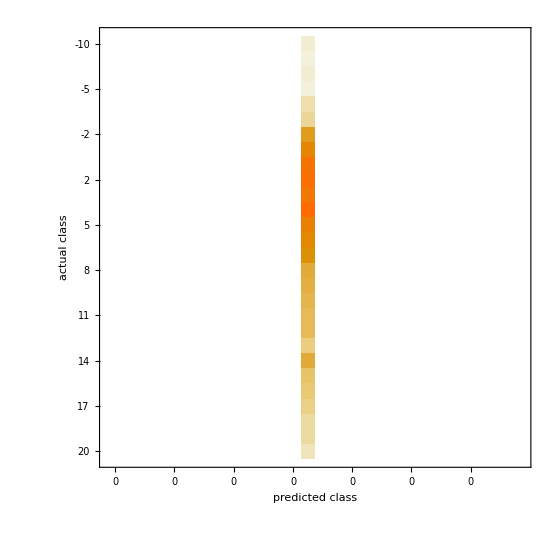

```mathematica
cm=ClassifierMeasurements[net,Select[trainingdata,#[[2]]≠0&]];
cm["ConfusionMatrixPlot"]
```

## all stock data training

```mathematica
szdirectory="/home/math/.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/";
allfiles=FileNames["*day",szdirectory];
```

```mathematica
trainingdata={};
Dynamic[N[watchinside/Length[allfiles]]]
(watchinside=#;
data=BinaryReadList[allfiles[[#]],{"Integer32","Integer32","Integer32","Integer32","Integer32","Real32","Integer32","Integer32"}];
data[[All,6]]=IntegerPart[data[[All,6]]];
If[Length[data]>500,
batch=Partition[data[[-300;;-20,{3,4,5,7}]],240,10];
pretrainingdata=(before=#[[;;200]];first=#[[201]];
Flatten[(N[#/first])&/@before]->If[(Max[#[[221;;-1,3]]]-first[[3]])/first[[3]]>0.033,1,-1])&/@batch;
AppendTo[trainingdata,Select[pretrainingdata,-20≤#[[2]]&&#[[2]]≤20&]]
];
)&/@Range[Length[allfiles]];
trainingdata=Flatten[trainingdata,1];
Clear[data,batch,pretrainingdata]
```

```mathematica
labels=Union[Flatten[trainingdata[[All,2]]]];
```

```mathematica
Sort[Counts[Flatten[trainingdata[[All,2]]]]]
```

<|1→4358,-1→6672|>

```mathematica
trainingdata//Length
```

11030

```mathematica
inputlength=trainingdata[[1,1]]//Length
outputlength=labels//Length
```

800

2

```mathematica
netgraph=NetGraph[{DotPlusLayer[10,"Input"->inputlength],Ramp,20,LogisticSigmoid,20,LogisticSigmoid,outputlength,LogisticSigmoid,SoftmaxLayer[]},{1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->9},"Output"->NetDecoder[{"Class",labels}]];
net=NetInitialize[netgraph];
netgraph
```

NetGraph[]

```mathematica
sampleamount=4000;
Clear[p];
Dynamic[p]
iter=1;
While[iter≤5,
trainingsample=Flatten[(label=#;RandomSample[Select[trainingdata,#[[2]]==label&],sampleamount])&/@labels];
net=NetTrain[net,trainingsample,MaxTrainingRounds->500,BatchSize->128,"ShowTrainingProgress"->True];
Beep[];
cm=ClassifierMeasurements[net,trainingsample];
p=cm["ConfusionMatrixPlot"];
iter++
];
ClearAll[cm,sampleamount,label]
```

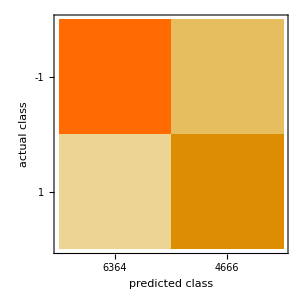

```mathematica
cm=ClassifierMeasurements[net,trainingdata];
cm["ConfusionMatrixPlot"]
Clear[cm]
```

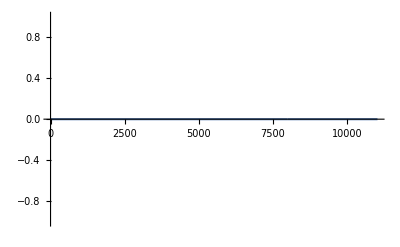

{0,0}

```mathematica
prefit=0;prefitlist={};
Dynamic[N[watchinside/Length[allfiles]]]
Dynamic[prefit]
positive=0;
negative=0;
(watchinside=#;
data=BinaryReadList[allfiles[[#]],{"Integer32","Integer32","Integer32","Integer32","Integer32","Real32","Integer32","Integer32"}];
data[[All,6]]=IntegerPart[data[[All,6]]];
If[Length[data]>500,
batch=Partition[data[[-300;;-20,{3,4,5,7}]],240,10];
(before=#[[;;220]];first=#[[220]];
If[net[Flatten[(N[#/first])&/@before]]==1,If[(Max[#[[231;;-1,3]]]-#[[220,3]])/(#[[220,3]])>0.033,prefit=prefit+0.033first[[3]];positive++,prefit=prefit+#[[-1,3]]-first[[3]];negative++]];
AppendTo[prefitlist,prefit];
)&/@batch
];
)&/@Range[Length[allfiles]];
ListLinePlot[prefitlist]
{positive,negative}
Clear[data,batch]
```

## min

```mathematica
szmindirectory="/home/math/.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/minline/";
shmindirectory="/home/math/.wine/drive_c/new_xdzq_tyrz/vipdoc/sh/minline/";
minstock[str_]:=If[StringStartsQ[str,"sz"],szmindirectory~~str~~".lc1",shmindirectory~~str~~".lc1"]
```

```mathematica
head={"day","min","O","H","L","C","Amount","Vol","flag"};
data=BinaryReadList[minstock["sz000002"],{"Integer16","Integer16","Real32","Real32","Real32","Real32","Real32","Integer32","Integer32"}];
data[[All,7]]=IntegerPart[data[[All,7]]];
data[[All,1]]=(10000(2004+Floor[#/2048])+100Floor[Mod[#,2048]/100]+Mod[Mod[#,2048],100])&/@data[[All,1]];
data[[All,2]]=(100*Floor[#/60]+Mod[#,60])&/@data[[All,2]];
TableForm[data[[-50;;-1]],TableHeadings->{None,head}]
```

day | min | O | H | L | C | Amount | Vol | flag
20180322 | 1411 | 31.33 | 31.37 | 31.33 | 31.36 | 2242339 | 71500 | 0
20180322 | 1412 | 31.36 | 31.36 | 31.33 | 31.34 | 2345094 | 74800 | 0
20180322 | 1413 | 31.36 | 31.36 | 31.31 | 31.32 | 2697181 | 86100 | 0
20180322 | 1414 | 31.32 | 31.35 | 31.3 | 31.31 | 3063016 | 97800 | 0
20180322 | 1415 | 31.31 | 31.33 | 31.3 | 31.3 | 4026889 | 128600 | 0
20180322 | 1416 | 31.33 | 31.34 | 31.3 | 31.34 | 2276537 | 72700 | 0
20180322 | 1417 | 31.31 | 31.34 | 31.3 | 31.31 | 4182984 | 133600 | 0
20180322 | 1418 | 31.33 | 31.36 | 31.33 | 31.33 | 1692377 | 54000 | 0
20180322 | 1419 | 31.35 | 31.38 | 31.33 | 31.36 | 2668318 | 85100 | 0
20180322 | 1420 | 31.36 | 31.41 | 31.36 | 31.41 | 3277491 | 104400 | 0
20180322 | 1421 | 31.4 | 31.45 | 31.4 | 31.44 | 6070309 | 193200 | 0
20180322 | 1422 | 31.44 | 31.45 | 31.4 | 31.4 | 3419852 | 108800 | 0
20180322 | 1423 | 31.4 | 31.4 | 31.31 | 31.33 | 3833127 | 122300 | 0
20180322 | 1424 | 31.33 | 31.35 | 31.3 | 31.34 | 2145470 | 68500 | 0
20180322 | 1425 | 31.34 | 31.34 | 31.31 | 31.33 | 2559513 | 81700 | 0
20180322 | 1426 | 31.32 | 31.36 | 31.31 | 31.36 | 2792495 | 89100 | 0
20180322 | 1427 | 31.35 | 31.37 | 31.32 | 31.33 | 4416038 | 140900 | 0
20180322 | 1428 | 31.33 | 31.33 | 31.3 | 31.31 | 4928008 | 157400 | 0
20180322 | 1429 | 31.3 | 31.35 | 31.3 | 31.34 | 3708133 | 118400 | 0
20180322 | 1430 | 31.34 | 31.36 | 31.3 | 31.35 | 3005305 | 95900 | 0
20180322 | 1431 | 31.34 | 31.38 | 31.32 | 31.32 | 1338650 | 42700 | 0
20180322 | 1432 | 31.34 | 31.34 | 31.3 | 31.31 | 1819482 | 58100 | 0
20180322 | 1433 | 31.31 | 31.32 | 31.3 | 31.3 | 1377587 | 44000 | 0
20180322 | 1434 | 31.3 | 31.34 | 31.3 | 31.3 | 3509746 | 112100 | 0
20180322 | 1435 | 31.31 | 31.31 | 31.26 | 31.26 | 3808495 | 121700 | 0
20180322 | 1436 | 31.26 | 31.27 | 31.25 | 31.25 | 1562691 | 50000 | 0
20180322 | 1437 | 31.25 | 31.26 | 31.25 | 31.26 | 2565748 | 82100 | 0
20180322 | 1438 | 31.26 | 31.32 | 31.26 | 31.28 | 2386981 | 76300 | 0
20180322 | 1439 | 31.27 | 31.3 | 31.27 | 31.27 | 1388684 | 44400 | 0
20180322 | 1440 | 31.27 | 31.27 | 31.25 | 31.25 | 4229169 | 135300 | 0
20180322 | 1441 | 31.25 | 31.26 | 31.25 | 31.25 | 10153253 | 324900 | 0
20180322 | 1442 | 31.25 | 31.26 | 31.24 | 31.25 | 5912209 | 189200 | 0
20180322 | 1443 | 31.23 | 31.23 | 31.18 | 31.19 | 4362454 | 139800 | 0
20180322 | 1444 | 31.19 | 31.2 | 31.18 | 31.2 | 4060672 | 130200 | 0
20180322 | 1445 | 31.22 | 31.22 | 31.2 | 31.22 | 2643971 | 84700 | 0
20180322 | 1446 | 31.23 | 31.23 | 31.21 | 31.23 | 3000467 | 96100 | 0
20180322 | 1447 | 31.23 | 31.26 | 31.23 | 31.25 | 4162408 | 133200 | 0
20180322 | 1448 | 31.25 | 31.27 | 31.25 | 31.26 | 4700274 | 150400 | 0
20180322 | 1449 | 31.25 | 31.26 | 31.24 | 31.24 | 9230144 | 295400 | 0
20180322 | 1450 | 31.24 | 31.24 | 31.21 | 31.21 | 3634990 | 116400 | 0
20180322 | 1451 | 31.21 | 31.22 | 31.2 | 31.21 | 2493747 | 79900 | 0
20180322 | 1452 | 31.21 | 31.22 | 31.2 | 31.2 | 3822775 | 122500 | 0
20180322 | 1453 | 31.21 | 31.21 | 31.2 | 31.2 | 3232729 | 103600 | 0
20180322 | 1454 | 31.2 | 31.2 | 31.18 | 31.18 | 4949596 | 158700 | 0
20180322 | 1455 | 31.18 | 31.19 | 31.17 | 31.17 | 5228465 | 167700 | 0
20180322 | 1456 | 31.18 | 31.18 | 31.16 | 31.16 | 4413388 | 141600 | 0
20180322 | 1457 | 31.17 | 31.18 | 31.17 | 31.18 | 4904125 | 157300 | 0
20180322 | 1458 | 31.18 | 31.18 | 31.18 | 31.18 | 215142 | 6900 | 0
20180322 | 1459 | 31.18 | 31.18 | 31.18 | 31.18 | 0 | 0 | 0
20180322 | 1500 | 31.18 | 31.18 | 31.18 | 31.18 | 3495278 | 112100 | 0